# Initialization

## Definitions

```mathematica
ρ[i_,j_]:=If[i==j,0,If[i<j,ρR[i,j]+ⅈ ρI[i,j],ρR[j,i]-ⅈ ρI[j,i]]]
ρhatinv[i_,j_]:=Inverse[Table[sqrtd[Min[m,n],Max[m,n]]ρ[m,n],{m,4},{n,4}]][[i,j]]
χbχ[i_,j_]:=If[i==j,χbχR[i,j],If[i<j,χbχR[i,j]+ⅈ χbχI[i,j],χbχR[j,i]-ⅈ χbχI[j,i]]]

sub=Flatten[{{Conjugate[ρR[i_,j_]]:>ρR[i,j]}, {Conjugate[ρI[i_,j_]]:>ρI[i,j]}, {Conjugate[χbχR[i_,j_]]:>χbχR[i,j]}, {Conjugate[χbχI[i_,j_]]:>χbχI[i,j]}, {sqrtd[i_,j_]:>sqrtd[Min[i,j],Max[i,j]]}, {Conjugate[sqrtd[i_,j_]]:>sqrtd[i,j]}, {Conjugate[g]->g}}];
```

```mathematica
subr={sqrtd[1,2]->1/(√rr)(sqrtd[1,4]sqrtd[2,3])/sqrtd[3,4],sqrtYdotY[1,2]->1/(√rr)(sqrtYdotY[1,4]sqrtYdotY[2,3])/sqrtYdotY[3,4] x[{x1,x2}]((x[{x1,x4}]x[{x2,x3}])/x[{x3,x4}])^-1};

subzzbααb={sqrtd[1,2]->(sqrtd[1,3] sqrtd[2,4])/(√zzboverααb sqrtd[3,4]),sqrtd[1,4]->(sqrtd[1,3] sqrtd[2,4])/(√oneminuszoneminuszboveroneminusαoneminusαb sqrtd[2,3]),sqrtYdotY[1,2]->(sqrtYdotY[1,3] sqrtYdotY[2,4])/(√zzboverααb sqrtYdotY[3,4])x[{x1,x2}]((x[{x1,x3}]x[{x2,x4}])/x[{x3,x4}])^-1,sqrtYdotY[1,4]->(sqrtYdotY[1,3] sqrtYdotY[2,4])/(√oneminuszoneminuszboveroneminusαoneminusαb sqrtYdotY[2,3])x[{x1,x4}]((x[{x1,x3}]x[{x2,x4}])/x[{x2,x3}])^-1};


{zzboverααb==((sqrtd[1,3] sqrtd[2,4])/(sqrtd[1,2] sqrtd[3,4]))^2,oneminuszoneminuszboveroneminusαoneminusαb==((sqrtd[1,3] sqrtd[2,4])/(sqrtd[1,4] sqrtd[2,3]))^2}/.subzzbααb//Union
```

{True}

```mathematica
simplest4pt={sqrtd[1,3]->0,sqrtd[2,4]->0,YdotY[1,3]->0,YdotY[2,4]->0};
```

```mathematica
vars:=DeleteCases[Table[{{ρR[i,j]}, {ρI[i,j]}},{i,m},{j,i+1,m}]//Flatten,0]
m=4;
vars4=vars;
Clear[m]
```

## Generalities

```mathematica
(* generalized Kronecker delta *)
genKro[list1_,list2_]:=If[Sort[list1]==Sort[list2],Signature[list1]Signature[list2],0]

(* Kronecker delta *)
SetAttributes[δ,Orderless]

(* replace Kronecker deltas (use with /. and not with //. *)
aSum:=((expr_. δ[a_,i_]):>If[a===i,expr N,expr/.a->i])
```

```mathematica
(* fermionic propagator *)
propagatorStandard[Subscript[χb[i_], i1_],Subscript[χ[j_], i2_]]:=-ⅈ/2 δ[i1,i2] Subscript[ρhatinv, i,j]
propagatorStandard[Subscript[χ[i_], i1_],Subscript[χb[j_], i2_]]:=-propagatorStandard[Subscript[χb[j], i2],Subscript[χ[i], i1]]
propagatorStandard[Subscript[χ[i_], i1_],Subscript[χ[j_], i2_]]:=0
propagatorStandard[Subscript[χb[i_], i1_],Subscript[χb[j_], i2_]]:=0

(* LO  contractions *)
contractionFree[list_]:=If[OddQ[Length[list]],0,If[Length[list]==0,1,∑_(ii=2)^Length[list] (-1)^ii propagatorStandard[list[[1]],list[[ii]]]contractionFree[Drop[Drop[list,{ii}],1]]]]
```

```mathematica
(* use symmetries *)
sub1=Flatten[{{II[list_]:>II[Sort[list]]}, {Y[list_]:>Y[Sort[list]]}, {X[list_]:>X[Sort[list]]}, {F[{a_,b_,c_,d_}]:>Signature[{a,b}]Signature[{c,d}]F[Flatten[{Sort[{a,b}],Sort[{c,d}]}]]}}];
sub2={F[{a_,b_,c_,d_}]:>If[a===c,F[{a,Sort[{b,d}][[1]],c,Sort[{b,d}][[2]]}],If[Sort[{a,c}]==={a,c},F[{a,b,c,d}],F[{c,d,a,b}]]]};
```

## Functions Y,X,F in point-splitting regularization

```mathematica
YY[list_]:=
Module[{output},

orderedList=(Y[list]//.sub1)[[1]];
numberIndependent=Length[Union[orderedList]];

If[numberIndependent==1 || numberIndependent==3 ,output=Y[orderedList]];

If[numberIndependent==2,{

While[orderedList[[1]]=!=orderedList[[2]],
orderedList=RotateLeft[orderedList,1];
];

one=orderedList[[1]];
two=orderedList[[3]];
output=-II[{one,two}]/(16 π^2)(Log[ϵ^2/x[{one,two}]^2]-2);
}];

output//.sub1//.{x[list2_]:>x[Sort[list2]]}

]
```

```mathematica
XX[list_]:=
Module[{output},

orderedList=(X[list]//.sub1)[[1]];
numberIndependent=Length[Union[orderedList]];

If[numberIndependent==1 || numberIndependent==4  ||(numberIndependent==2 && (MemberQ[{orderedList},{x_,x_,x_,y_}]||MemberQ[{orderedList},{y_,x_,x_,x_}])),output=X[orderedList]];

If[numberIndependent==2 && MemberQ[{orderedList},{x_,x_,y_,y_}],{

While[orderedList[[1]]=!=orderedList[[2]],
orderedList=RotateLeft[orderedList,1];
];

one=orderedList[[1]];
two=orderedList[[3]];
output=-II[{one,two}]^2/(8 π^2)(Log[ϵ^2/x[{one,two}]^2]-1);
}];

If[numberIndependent==3,{

While[orderedList[[1]]=!=orderedList[[2]],
orderedList=RotateLeft[orderedList,1];
];

one=orderedList[[1]];
two=orderedList[[3]];
three=orderedList[[4]];
output=-(II[{one,two}]II[{one,three}])/(16 π^2)(Log[(ϵ^2 x[{two,three}]^2)/(x[{one,two}]^2 x[{one,three}]^2)]-2);
}];

output//.sub1//.{x[list2_]:>x[Sort[list2]]}

]
```

```mathematica
FF[list_]:=
Module[{output},

If[(F[list]//.sub1)===0,output=0,{

overallSign=(F[list]//.sub1)/.{F[list2_]:>1};
orderedList=(overallSign F[list]//.sub1)[[1]];
numberIndependent=Length[Union[orderedList]];

If[numberIndependent==4,{
one=orderedList[[1]];
two=orderedList[[2]];
three=orderedList[[3]];
four=orderedList[[4]];

G[one_,two_,three_]:=Y[{one,two,three}](1/II[{one,three}]-1/II[{one,two}]);
output=X[orderedList](1/(II[{one,three}]II[{two,four}])-1/(II[{one,four}]II[{two,three}]))+G[one,three,four]-G[two,three,four]+G[three,one,two]-G[four,one,two];
}];

If[numberIndependent==2,
one=orderedList[[1]];
two=orderedList[[2]];
output=-1/(8 π^2)(Log[ϵ^2/x[{one,two}]^2]-3);
];

If[numberIndependent==3 && MemberQ[{orderedList},{one_,two_,one_,three_}],{
one=orderedList[[1]];
two=orderedList[[2]];
three=orderedList[[4]];
output=-1/(16 π^2)(Log[ϵ^2/x[{two,three}]^2]-2)+Y[{one,two,three}](1/II[{one,two}]+1/II[{one,three}]-2/II[{two,three}]);
}];

If[numberIndependent==3 && MemberQ[{orderedList},{one_,two_,three_,one_}],{
one=orderedList[[1]];
two=orderedList[[2]];
three=orderedList[[3]];
output=1/(16 π^2)(Log[ϵ^2/x[{two,three}]^2]-2)-Y[{one,two,three}](1/II[{one,two}]+1/II[{one,three}]-2/II[{two,three}]);
}];

If[numberIndependent==3 && MemberQ[{orderedList},{two_,one_,one_,three_}],{
one=orderedList[[2]];
two=orderedList[[1]];
three=orderedList[[4]];
output=1/(16 π^2)(Log[ϵ^2/x[{two,three}]^2]-2)-Y[{one,two,three}](1/II[{one,two}]+1/II[{one,three}]-2/II[{two,three}]);
}];

If[numberIndependent==3 && MemberQ[{orderedList},{two_,one_,three_,one_}],{
one=orderedList[[2]];
two=orderedList[[1]];
three=orderedList[[3]];
output=-1/(16 π^2)(Log[ϵ^2/x[{two,three}]^2]-2)+Y[{one,two,three}](1/II[{one,two}]+1/II[{one,three}]-2/II[{two,three}]);
}];

}];

overallSign output//.sub1//.{x[list2_]:>x[Sort[list2]]}

]
```

```mathematica
(* check properties *)
```

```mathematica
tmp=Tuples[{1,2,3},3];
Table[(Y[tmp[[i]]]//.sub1//.Y->YY)==YY[tmp[[i]]],{i,Length[tmp]}]//Union

tmp=Tuples[{1,2,3,4},4][[1;;23]]
Table[(X[tmp[[i]]]//.sub1//.X->XX)==XX[tmp[[i]]],{i,Length[tmp]}]//Union
Table[If[(F[tmp[[i]]]//.sub1)===0,0,F[tmp[[i]]]//.sub1//.F->FF]== FF[tmp[[i]]],{i,Length[tmp]}]//Simplify//Union

FF[{1,2,1,3}]==FF[{2,1,3,1}]


Clear[tmp]
```

{True}

{{1,1,1,1},{1,1,1,2},{1,1,1,3},{1,1,1,4},{1,1,2,1},{1,1,2,2},{1,1,2,3},{1,1,2,4},{1,1,3,1},{1,1,3,2},{1,1,3,3},{1,1,3,4},{1,1,4,1},{1,1,4,2},{1,1,4,3},{1,1,4,4},{1,2,1,1},{1,2,1,2},{1,2,1,3},{1,2,1,4},{1,2,2,1},{1,2,2,2},{1,2,2,3}}

{True}

{True}

True

# Derivation

## Step 3

```mathematica
m=3;
Table[{vars[[i]],-∞,∞},{i,Length[vars]}];

Sum[-N/g^2 ρ[i,j]ρ[j,i]+2ⅈ sqrtd[i,j] ρ[i,j]χbχ[j,i],{i,m},{j,m}]//.sub//Simplify;
Integrate[Exp[%],Sequence@@%%,Assumptions->N>0 && g>0]/(tmp=Integrate[Exp[%/.{sqrtd[i_,j_]->0}],Sequence@@%%,Assumptions->N>0 && g>0])==Exp[-g^2/N Sum[(1-i,j)sqrtd[i,j]^2 χbχ[i,j]χbχ[j,i],{i,m},{j,m}]]//.sub//Simplify

tmp==((g^2 π)/(2 N))^(m(m-1)/2)

Clear[m]
```

True

True

## Saddle-pt equations

```mathematica
m=4;
Table[{vars[[i]],-∞,∞},{i,Length[vars]}];

N Sum[-(1-i,j)1/g^2 ρρ[i,j]ρρ[j,i],{i,m},{j,m}]+N Log[Det[Table[-2ⅈ (1-i,j)ρρ[i,j]sqrtd[i ,j],{i,m},{j,m}]]];
Table[ρρ[i,j]sqrtd[i,j],{i,m},{j,m}]//Inverse;
Table[D[%%,ρρ[j,i]]/(-(2N)/g^2 ρρ[i,j]+N sqrtd[i,j] %[[i,j]])==1,{i,2,m},{j,i-1}]/.{ρρ[i_,i_]:>0}/.{sqrtd[i_,j_]:>sqrtd[Min[i,j],Max[i,j]]}//Simplify//Flatten//Union

Clear[m,tmp]
```

{True}

# 1-loop building blocks (m=4, no field rotation)

## <O_O^S>

```mathematica
tmp1=contractionFree[{Subscript[χ[k1], i1],Subscript[χb[k1], i2],Subscript[χ[k2], i2],Subscript[χb[k2], i1]}]//Expand;
Do[
tmp1=tmp1//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_ :>If[n==2,N^(n/2),NaN]}/.aSum,
20];

tmp2=contractionFree[{Subscript[χ[k1], i1],Subscript[χb[k1], i1],Subscript[χ[k2], i2],Subscript[χb[k2], i2]}]//Expand;
Do[
tmp2=tmp2//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_ :>If[n==2,N^(n/2),NaN]}/.aSum,
20];

OSO=λ^2/N(λ/N)^-2 (λ/(2N))^2 Sum[(1-k1,k2)(Y[{Subscript[x, k1],Subscript[x, k1],Subscript[x, k2]}]+Y[{Subscript[x, k1],Subscript[x, k2],Subscript[x, k2]}])sqrtYdotY[k1,k2]^2(-tmp1+1/N tmp2//Expand),{k1,4},{k2,4}];

Clear[tmp1,tmp2]
```

## <O_X^S>

```mathematica
tmp1=contractionFree[{Subscript[χ[k1], i1],Subscript[χb[k1], i2],Subscript[χ[k3], i2],Subscript[χb[k3], i3],Subscript[χ[k4], i3],Subscript[χb[k4], i4],Subscript[χ[k2], i4],Subscript[χb[k2], i1]}]//Expand;
Do[
tmp1=tmp1//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_ :>If[n==2,N^(n/2),NaN]}/.aSum,
20];

tmp2=contractionFree[{Subscript[χ[k1], i1],Subscript[χb[k1], i2],Subscript[χ[k3], i2],Subscript[χb[k3], i3],Subscript[χ[k2], i3],Subscript[χb[k2], i4],Subscript[χ[k4], i4],Subscript[χb[k4], i1]}]//Expand;
Do[
tmp2=tmp2//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_ :>If[n==2,N^(n/2),NaN]}/.aSum,
20];

OSX=λ^3/N^3(λ/N)^-4 (λ/(2N))^4 Sum[(1-k1,k2)(1-k3,k4)X[{Subscript[x, k1],Subscript[x, k2],Subscript[x, k3],Subscript[x, k4]}] sqrtYdotY[k1,k2]^2 sqrtYdotY[k3,k4]^2(-tmp1+tmp2//Expand),{k1,4},{k2,4},{k3,4},{k4,4}];

Clear[tmp1,tmp2]
```

## <O_H^S>

```mathematica
tmp1=contractionFree[{Subscript[χ[k1], i1],Subscript[χb[k1], i2],Subscript[χ[k2], i2],Subscript[χb[k2], i3],Subscript[χ[k3], i3],Subscript[χb[k3], i4],Subscript[χ[k4], i4],Subscript[χb[k4], i1]}]//Expand;
Do[
tmp1=tmp1//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_ :>If[n==2,N^(n/2),NaN]}/.aSum,
20];

OSH=λ^3/N^3(λ/N)^-4 (λ/(2N))^4 Sum[(1-k1,k2)(1-k3,k4)II[{Subscript[x, k1],Subscript[x, k2]}]II[{Subscript[x, k3],Subscript[x, k4]}]F[{Subscript[x, k1],Subscript[x, k2],Subscript[x, k3],Subscript[x, k4]}] sqrtYdotY[k1,k2]^2 sqrtYdotY[k3,k4]^2(-tmp1//Expand),{k1,4},{k2,4},{k3,4},{k4,4}];

Clear[tmp1]
```

## Sum

```mathematica
OSOXH=A OSO+B OSX+C OSH/.{λ->16 π^2 g^2}/.{sqrtYdotY[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]}/.{Subscript[x, 1]->x1,Subscript[x, 2]->x2,Subscript[x, 3]->x3,Subscript[x, 4]->x4}//.sub1//.sub2/.{F[list_]:>FF[list]};

(* non-conformal + conformal parts *)
(OSOXH-(OSOXH/.{X[{x1,x2,x3,x4}]->0}))+(OSOXH/.X[{x1,x2,x3,x4}]->0)==OSOXH/.Flatten[{{g->RandomReal[]}, {N->RandomReal[]}, {ϵ->RandomReal[]}, {A->RandomReal[]}, {B->RandomReal[]}, {C->RandomReal[]}}]//Expand//Chop
```

True

# 4-pt

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ e^-NS_eff

```mathematica
NN=3;

(* integrand *)
exponent=N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]/.N->NN;
fieldDepFactor=Exp[N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]]/.N->NN/.{sqrtd[i_,j_]:>sqrtd[Min[i,j],Max[i,j]]}//CoefficientRules[#,vars4]&//Simplify//FromCoefficientRules[#,vars4]&;
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtd[1,2]^2)^N)(N!(λ/(8 π^2 N)sqrtd[3,4]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))/.N->NN//Simplify;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[vars4],i++,
fieldDepFactor=fieldDepFactor/.{vars4[[i]]->ϵ^2 vars4[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

(* integration *)
tmp=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
For[i=1,i≤Length[tmp],i++,
For[j=1,j≤Length[vars4],j++,
tmp[[i]]=If[(tmp[[i]]/.{vars4[[j]]->0})===0,tmp[[i]]/.{vars4[[j]]^n_:>(-Coefficient[exponent,vars4[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp[[i]](√π)/(√(-Coefficient[exponent,vars4[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp]}],i},""]];

tmp=fieldIndepFactor Total[tmp]//PowerExpand//Simplify;

(* check *)
1/(NN!)Sum[If[0≤k0+k1+2 k2+2 k3+2 k4≤NN,(((sqrtd[1,3]sqrtd[2,4])^2/(sqrtd[1,2]sqrtd[3,4])^2)^(k0+k2+k4) ((sqrtd[1,4]sqrtd[2,3])^2/(sqrtd[1,2]sqrtd[3,4])^2)^(k1+k2+k3) ((k1+k2+k3)!)^2 ((k0+k2+k4)!)^2 ((-k0-k1-2 k2-k3-k4+NN)!)^2)/(k0!k1! (k2!)^2 (k3!)^2 (k4!)^2  (-k0-k1-2 k2-2 k3-2 k4+NN)!),0],{k0,0,NN},{k1,0,NN},{k2,0,NN},{k3,0,NN},{k4,0,NN}]==tmp//Simplify

1/(NN!)Sum[(((sqrtd[1,3]sqrtd[2,4])^2/(sqrtd[1,2]sqrtd[3,4])^2)^k0 ((sqrtd[1,4]sqrtd[2,3])^2/(sqrtd[1,2]sqrtd[3,4])^2)^k1 (k0!)^2(k1!)^2 ((NN-k0-k1)!)^2)/((k2!)^2 (k1-k2-k3)! (k3!)^2 (k0-k2-k4)! (NN-k0-k1-k3-k4)! (k4!)^2),{k0,0,NN},{k1,0,NN},{k2,0,NN},{k3,0,NN},{k4,0,NN-k0-k1-k3}]==tmp//Simplify

1/(NN!)Sum[((sqrtd[1,3]sqrtd[2,4])^2/(sqrtd[1,2]sqrtd[3,4])^2)^(NN-l12) ((sqrtd[1,3]sqrtd[2,4])^2/(sqrtd[1,4]sqrtd[2,3])^2)^(l12+l13-NN)((l12!l13!(NN-l12-l13)!)/((l13-numrl)!(NN-l12-l13-numpn)!(numrl-numkrl)!))^2 1/((-NN+2l12+numrl+numpn)!numkrl!(numpn-numrl+numkrl)!),{l12,0,NN},{l13,0,NN-l12},{numrl,0,l13},{numpn,Max[0,NN-2l12-numrl],NN-l12-l13},{numkrl,Max[0,numrl-numpn],numrl}]==tmp//Simplify

Clear[NN]
```

True

True

True

«1 more identical outputs»

## Saddle-pt of ∫dρ e^-NS_eff [only major cases]

```mathematica
Clear[a,b,c]

(* action *)
N Sum[-(1-i,j)1/g^2 ρρ[i,j]ρρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub;
tmp=%/.{ρρ->ρ}/.Flatten[{{ρR[i_,j_]:>r[i,j]Cos[θ[i,j]]}, {ρI[i_,j_]:>r[i,j]Sin[θ[i,j]]}}]//ExpandAll//Simplify;

(* variables *)
tmp2={r[1,2],r[1,3],r[1,4],r[2,3],r[2,4],r[3,4],θ[1,2],θ[1,3],θ[1,4],θ[2,3],θ[2,4],θ[3,4]};
Length[tmp2]==12

(* equations *)
tmp3=Table[D[tmp,tmp2[[i]]],{i,Length[tmp2]}]//Simplify;
g^2/(32N)(Det[Table[-2ⅈ (1-i,j)ρρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]/.sub/.{ρρ->ρ}/.Flatten[{{ρR[i_,j_]:>r[i,j]Cos[θ[i,j]]}, {ρI[i_,j_]:>r[i,j]Sin[θ[i,j]]}}]//FullSimplify)%//Simplify;
tmp=%/.Flatten[{{θ[1,2]-θ[1,4]+θ[2,3]+θ[3,4]->a}, {θ[1,2]-θ[1,3]+θ[2,4]-θ[3,4]->b}, {θ[1,3]-θ[1,4]-θ[2,3]+θ[2,4]->c}}]//Simplify;

(Table[D[tmp,tmp2[[i]]],{i,7,12}]//Flatten//Union)=={0}

tmp=Table[tmp[[i]]==0,{i,Length[tmp]}]//Simplify;

(* extra equations *)
tmp4=Join[{g≠0},Table[{sqrtd[i,j]≠0,r[i,j]≠-g/(√2)},{i,4},{j,i+1,4}]//Flatten]//Union;
```

True

True

```mathematica
(* solution with non-zero parameters *)
```

```mathematica
tmp;
Join[%,tmp4];
Solve[%,tmp2]//Simplify//Union//MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

({r[1,2]→0,r[1,3]→0,r[1,4]→0}
{r[1,2]→0,r[1,3]→0,r[2,3]→0}
{r[1,2]→0,r[1,4]→0,r[2,4]→0}
{r[1,2]→0,r[2,3]→0,r[2,4]→0}
{r[1,3]→0,r[1,4]→0,r[3,4]→0}
{r[1,3]→0,r[2,3]→0,r[3,4]→0}
{r[1,4]→0,r[2,4]→0,r[3,4]→0}
{r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[2,3]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[2,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→g/(√2),r[2,3]→0}
{r[1,2]→0,r[1,3]→0,r[2,3]→0,r[2,4]→0}
{r[1,2]→0,r[1,3]→0,r[2,3]→0,r[3,4]→0}
{r[1,2]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0}
{r[1,2]→0,r[1,4]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,3]→0,r[1,4]→0,r[2,3]→0,r[3,4]→0}
{r[1,3]→0,r[1,4]→0,r[2,4]→0,r[3,4]→0}
{r[1,3]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[2,3]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→g/(√2),r[2,3]→0,r[2,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→g/(√2),r[2,3]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→g/(√2),r[1,4]→0,r[2,3]→0,r[2,4]→0}
{r[1,2]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,3]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→g/(√2),r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→0,r[1,4]→g/(√2),r[2,3]→g/(√2),r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→g/(√2),r[1,4]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→0,r[1,3]→g/(√2),r[1,4]→0,r[2,3]→0,r[2,4]→g/(√2),r[3,4]→0}
{r[1,2]→g/(√2),r[1,3]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0,r[3,4]→0}
{r[1,2]→g/(√2),r[1,3]→0,r[1,4]→0,r[2,3]→0,r[2,4]→0,r[3,4]→g/(√2)})

```mathematica
({{{r[1,2]->0,r[1,3]->0,r[1,4]->0}}, {{r[1,2]->0,r[1,3]->0,r[2,3]->0}}, {{r[1,2]->0,r[1,4]->0,r[2,4]->0}}, {{r[1,2]->0,r[2,3]->0,r[2,4]->0}}, {{r[1,3]->0,r[1,4]->0,r[3,4]->0}}, {{r[1,3]->0,r[2,3]->0,r[3,4]->0}}, {{r[1,4]->0,r[2,4]->0,r[3,4]->0}}, {{r[2,3]->0,r[2,4]->0,r[3,4]->0}}, {{r[1,2]->0,r[1,3]->0,r[1,4]->g/(√2),r[2,3]->g/(√2),r[2,4]->0,r[3,4]->0}}, {{r[1,2]->0,r[1,3]->g/(√2),r[1,4]->0,r[2,3]->0,r[2,4]->g/(√2),r[3,4]->0}}, {{r[1,2]->g/(√2),r[1,3]->0,r[1,4]->0,r[2,3]->0,r[2,4]->0,r[3,4]->g/(√2)}}});
```

```mathematica
(* non-acceptable solutions *)
```

```mathematica
Series[tmp3,{r[1,2],0,0},{r[1,3],0,0},{r[1,4],0,0}]//FullSimplify//Normal
```

{-(2 N Cos[θ[1,2]-θ[1,4]+θ[2,3]+θ[3,4]] r[3,4] sqrtd[1,2] sqrtd[3,4])/(r[1,4] r[2,3] sqrtd[1,4] sqrtd[2,3]),-(2 N Cos[θ[1,3]-θ[1,4]-θ[2,3]+θ[2,4]] r[2,4] sqrtd[1,3] sqrtd[2,4])/(r[1,4] r[2,3] sqrtd[1,4] sqrtd[2,3]),(2 N)/r[1,4],N (2/r[2,3]-(4 r[2,3])/g^2),-(4 N r[2,4])/g^2,-(4 N r[3,4])/g^2,0,0,0,0,0,0}

```mathematica
Series[tmp3,{r[1,2],0,0},{r[2,3],0,0},{r[1,3],0,0}]//FullSimplify//Normal
```

{-(2 N Cos[θ[1,2]-θ[1,3]+θ[2,4]-θ[3,4]] r[3,4] sqrtd[1,2] sqrtd[3,4])/(r[1,3] r[2,4] sqrtd[1,3] sqrtd[2,4]),(2 N)/r[1,3],-(4 N r[1,4])/g^2,-(2 N Cos[θ[1,3]-θ[1,4]-θ[2,3]+θ[2,4]] r[1,4] sqrtd[1,4] sqrtd[2,3])/(r[1,3] r[2,4] sqrtd[1,3] sqrtd[2,4]),N (2/r[2,4]-(4 r[2,4])/g^2),-(4 N r[3,4])/g^2,0,0,0,0,0,0}

```mathematica
(* solution with some zero parameters *)
```

```mathematica
(*Table[{a->π/2 i},{i,0,3}];
%/.{a->b};
%%/.{a->c};
Table[{a->π/2 i,b->π/2 j},{i,0,3},{j,0,3}]//Flatten[#,1]&;
%/.{b->c};
%%/.{a->b,b->c};
Table[{a->π/2 i,b->π/2 j,c->π/2 k},{i,0,3},{j,0,3},{k,0,3}]//Flatten[#,2]&;
tmp5=Join[%%%%%%%,%%%%%%,%%%%%,%%%%,%%%,%%,%];

For[i=1,i≤Length[tmp5],i++,{
Print[{tmp5[[i]]//MatrixForm,Solve[Join[tmp/.tmp5[[i]]//Simplify,tmp4],tmp2]//Simplify//Union//MatrixForm}]
}]
```

```mathematica
(* singular cross-ratio (z zb)/(α αb)=1 *)
```

```mathematica
tmp/.subzzbααb/.{zzboverααb->1}//Simplify;
Join[%,tmp4];
Solve[%,tmp2]//Simplify//Union//MatrixForm
```

$Aborted

```mathematica
(* singular cross-ratio ((1-z)(1-zb))/((1-α)(1-αb))=1 *)
```

```mathematica
tmp/.subzzbααb/.{oneminuszoneminuszboveroneminusαoneminusαb->1}//Simplify;
Join[%,tmp4];
Solve[%,tmp2]//Simplify//Union//MatrixForm
```

```mathematica
(* singular cross-ratio ((1-z)(1-zb))/((1-α)(1-αb))=((1-z)(1-zb))/((1-α)(1-αb)) *)
```

```mathematica
tmp/.subzzbααb/.{oneminuszoneminuszboveroneminusαoneminusαb->zzboverααb}//Simplify;
Join[%,tmp4];
Solve[%,tmp2]//Simplify//Union//MatrixForm
```

## Definitions for saddle-pt and integration

```mathematica
CartesianRadiusVariablesRnotOne={ρR[1,3],ρI[1,3],ρR[1,4],ρI[1,4],ρR[2,3],ρI[2,3],ρR[2,4],ρI[2,4],r[1,2],r[3,4]};
PolarVariablesRnotOne={θ[1,2],θ[3,4]};
VariablesRnotOne=Join[CartesianRadiusVariablesRnotOne,PolarVariablesRnotOne];
Length[VariablesRnotOne]==12

CartesianRadiusVariablesREqualOne={ρR[1,3],ρI[1,3],ρR[2,4],ρI[2,4],r,θ1,θ2,ξ};
PolarVariablesREqualOne={α,φ1,φ2,χ};
VariablesREqualOne=Join[CartesianRadiusVariablesREqualOne,PolarVariablesREqualOne];
Length[VariablesREqualOne]==12

fieldRotationRnotOne=Flatten[{{ρR[1,4]->(Cos[θ[1,2]+θ[3,4]] (ρI[1,4]-ρI[2,3])+Sin[θ[1,2]+θ[3,4]] (-ρR[1,4]+ρR[2,3]))/(√2)}, {ρI[1,4]->(Sin[θ[1,2]+θ[3,4]] (ρI[1,4]-ρI[2,3])+Cos[θ[1,2]+θ[3,4]] (ρR[1,4]-ρR[2,3]))/(√2)}, {ρR[2,3]->(ρI[1,4]+ρI[2,3])/(√2)}, {ρI[2,3]->(ρR[1,4]+ρR[2,3])/(√2)}}];
({ρR[1,4],ρI[1,4],ρR[2,3],ρI[2,3]}/.fieldRotationRnotOne/.Flatten[{{ρR[1,4]->(Cos[θ[1,2]+θ[3,4]] ρI[1,4])/(√2)+ρI[2,3]/(√2)-(Sin[θ[1,2]+θ[3,4]] ρR[1,4])/(√2)}, {ρI[1,4]->(Sin[θ[1,2]+θ[3,4]] ρI[1,4])/(√2)+(Cos[θ[1,2]+θ[3,4]] ρR[1,4])/(√2)+ρR[2,3]/(√2)}, {ρR[2,3]->-(Cos[θ[1,2]+θ[3,4]] ρI[1,4])/(√2)+ρI[2,3]/(√2)+(Sin[θ[1,2]+θ[3,4]] ρR[1,4])/(√2)}, {ρI[2,3]->-(Sin[θ[1,2]+θ[3,4]] ρI[1,4])/(√2)-(Cos[θ[1,2]+θ[3,4]] ρR[1,4])/(√2)+ρR[2,3]/(√2)}}])=={ρR[1,4],ρI[1,4],ρR[2,3],ρI[2,3]}//Simplify

simplest4pt=Flatten[{{sqrtd[1,3]->0}, {sqrtd[2,4]->0}, {sqrtYdotY[1,3]->0}, {sqrtYdotY[2,4]->0}}];
```

True

True

True

```mathematica
Clear[n,a]
Integrate[x^n Exp[a x^2],{x,-∞,∞},Assumptions->n∈Integers&&n≥1&&z<0&&a<0]//Simplify
```

1/2 (1+(-1)^n) (-a)^(-1/2-n/2) Gamma[(1+n)/2]

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian)e^-NS_eff

```mathematica
n=19;
```

```mathematica
(* Jacobian *)
```

```mathematica
jacobian=(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]);
```

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify;
tmp=%/.Flatten[{{ρR[1,3]->(Cos[θ[1,2]-θ[3,4]] (ρI[1,3]-ρI[2,4])+Sin[θ[1,2]-θ[3,4]] (-ρR[1,3]+ρR[2,4]))/(√2)}, {ρI[1,3]->(Sin[θ[1,2]-θ[3,4]] (ρI[1,3]-ρI[2,4])+Cos[θ[1,2]-θ[3,4]] (ρR[1,3]-ρR[2,4]))/(√2)}, {ρR[2,4]->(ρI[1,3]+ρI[2,4])/(√2)}, {ρI[2,4]->(ρR[1,3]+ρR[2,4])/(√2)}}]/.fieldRotationRnotOne/.Log[x_]:>Log[x//Simplify]//PowerExpand//Simplify;

(* no linear term in action *)
SeriesCoefficient[tmp,{u,0,1}]==0
```

True

```mathematica
(* integrand *)
exponent=u^2 SeriesCoefficient[tmp,{u,0,2}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

fieldDepFactor=Table[0,{i,n}];

Monitor[
Table[fieldDepFactor[[i]]=(SeriesCoefficient[jacobian(Exp[tmp-exponent-(tmp/.u->0)]//ExpandAll//Simplify//PowerExpand//Simplify),{u,0,i-1}]//Normal)/.u->1//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,Length[fieldDepFactor]}],
Row[{ProgressIndicator[i,{1,Length[fieldDepFactor]}],i},""]];

exponent=exponent/.u->1;

fieldDepFactor=Total[fieldDepFactor];

fieldIndepFactor=1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp/.u->0]/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}/.subzzbααb//PowerExpand)//ExpandAll//PowerExpand//Simplify//Distribute;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

(* simplify even powers *)
tmp2=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
Table[tmp2[[i]]=tmp2[[i]]//Simplify,{i,Length[tmp2]}],
Row[{ProgressIndicator[i,{1,Length[tmp2]}],i},""]];

fieldDepFactor=Total[tmp2];
```

-(4 N u^2 r[1,2]^2)/g^2-(4 N u^2 r[3,4]^2)/g^2-(2 N u^2 (1+√zzbaroverααbar) ρI[1,3]^2)/g^2-(2 N u^2 (√oneminuszoneminuszbaroveroneminusαoneminusαbar+√zzbaroverααbar) ρI[1,4]^2)/(g^2 √oneminuszoneminuszbaroveroneminusαoneminusαbar)+(2 N u^2 (-√oneminuszoneminuszbaroveroneminusαoneminusαbar+√zzbaroverααbar) ρI[2,3]^2)/(g^2 √oneminuszoneminuszbaroveroneminusαoneminusαbar)+(2 N u^2 (-1+√zzbaroverααbar) ρI[2,4]^2)/g^2-(2 N u^2 (1+√zzbaroverααbar) ρR[1,3]^2)/g^2-(2 N u^2 (√oneminuszoneminuszbaroveroneminusαoneminusαbar+√zzbaroverααbar) ρR[1,4]^2)/(g^2 √oneminuszoneminuszbaroveroneminusαoneminusαbar)+(2 N u^2 (-√oneminuszoneminuszbaroveroneminusαoneminusαbar+√zzbaroverααbar) ρR[2,3]^2)/(g^2 √oneminuszoneminuszbaroveroneminusαoneminusαbar)+(2 N u^2 (-1+√zzbaroverααbar) ρR[2,4]^2)/g^2

```mathematica
(* integration *)
tmp3=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];
```

True

```mathematica
tmp4=0tmp3;
tmp5=Series[fieldIndepFactor/N^5,{N,∞,3}];

Monitor[
For[i=1,i≤Length[tmp4],i++,
tmp4[[i]]=tmp5 Series[N^5 tmp3[[i]]//PowerExpand,{N,∞,3}]//Simplify;
],
Row[{ProgressIndicator[i,{1,Length[tmp4]}],i},""]];
```

```mathematica
DeleteCases[tmp4//Normal,0]//Total//Collect[#,N,Simplify]&;
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}]//Collect[#,N,Simplify]&;

%/.{zzboverααb->A,oneminuszoneminuszboveroneminusαoneminusαb->B}//Simplify
```

(B ((-1+A)^3 (A-B)^3-(2 A^2 (9 A^4-B^2+14 A^3 (1+B)+A^2 (1+22 B+B^2)))/N^3+(2 (-1+A) A^2 (A-B) (A+3 A^2+B+A B))/N^2-(2 (-1+A)^2 A^2 (A-B)^2)/N))/((-1+A)^4 (A-B)^4)

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian)e^-NS_eff (v2)

```mathematica
n=11;
```

```mathematica
(* Jacobian *)
```

```mathematica
jacobian=(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]);
```

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify;
tmp=%/.Flatten[{{ρR[1,3]->(Cos[θ[1,2]-θ[3,4]] (ρI[1,3]-ρI[2,4])+Sin[θ[1,2]-θ[3,4]] (-ρR[1,3]+ρR[2,4]))/(√2)}, {ρI[1,3]->(Sin[θ[1,2]-θ[3,4]] (ρI[1,3]-ρI[2,4])+Cos[θ[1,2]-θ[3,4]] (ρR[1,3]-ρR[2,4]))/(√2)}, {ρR[2,4]->(ρI[1,3]+ρI[2,4])/(√2)}, {ρI[2,4]->(ρR[1,3]+ρR[2,4])/(√2)}}]/.fieldRotationRnotOne/.{θ[1,2]->0,θ[3,4]->0}/.Log[x_]:>Log[x//Simplify]//PowerExpand//Simplify;

(* no linear term in action *)
SeriesCoefficient[tmp,{u,0,1}]==0
```

True

```mathematica
(* integrand *)
exponent=u^2 SeriesCoefficient[tmp,{u,0,2}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;


tmp2a=jacobian Series[(1+Sum[a[i] u^i,{i,3,n-1}])^N,{u,0,n-1}]//PowerExpand//Normal//CoefficientRules[#,Table[a[i],{i,0,n-1}]]&//Simplify//FromCoefficientRules[#,Table[a[i],{i,0,n-1}]]&//Series[#,{u,0,n-1}]&;


tmp2b=Series[Exp[(tmp-exponent-(tmp/.u->0))/N//Simplify]//Simplify,{u,0,n-1}];
Normal[Series[%,{u,0,2}]]==1

Print["Calculating tmp2b"];
Monitor[
tmp2b=Table[a[i]->(SeriesCoefficient[tmp2b,i]//PowerExpand//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&),{i,n-1,0,-1}],
Row[{ProgressIndicator[i,{0,n-1}],i},""]];

fieldDepFactor=Table[0,{i,n}];

time=AbsoluteTime[];

Print["Calculating fieldDepFactor"];
Monitor[
For[i=Length[fieldDepFactor],i≥5,i--,{

tmp2c=SeriesCoefficient[tmp2a,i-1]//CoefficientRules[#,Table[a[i],{i,0,n-1}]]&//Simplify//FromCoefficientRules[#,Table[a[i],{i,0,n-1}]]&;

tmp2d=List@@tmp2c;
Print[Total[tmp2d]==tmp2c];

Monitor[
For[j=Length[tmp2d],j≥1,j--,{
tmp2d[[j]]=tmp2d[[j]]/.tmp2b//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
Print["Case (i,j)=(",i,",",j,") done at ",Floor[(AbsoluteTime[]-time)/60^2]//Chop,"h ",NumberForm[(AbsoluteTime[]-time-60^2 Floor[(AbsoluteTime[]-time)/60^2])/60,{∞,1}],"m"];
}],
Row[{ProgressIndicator[j,{1,Length[tmp2d]}],j},""]];

fieldDepFactor[[i]]=Total[tmp2d];

}],
Row[{ProgressIndicator[i,{4,Length[fieldDepFactor]}],i},""]];

For[i=4,i≥1,i--,
fieldDepFactor[[i]]=SeriesCoefficient[tmp2a,i-1]/.tmp2b//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
]

exponent=exponent/.u->1;

fieldDepFactor=Total[fieldDepFactor];

fieldIndepFactor=1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp/.u->0]/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}/.subzzbααb//PowerExpand)//ExpandAll//PowerExpand//Simplify//Distribute;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
Print["Discarding odd powers"];
Monitor[
Table[fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]},{i,Length[CartesianRadiusVariablesRnotOne]}],
Row[{ProgressIndicator[i,{1,Length[CartesianRadiusVariablesRnotOne]}],i},""]];

(* simplify even powers *)
Print["Simplifying even powers"];
tmp2=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
Table[tmp2[[i]]=tmp2[[i]]//Simplify,{i,Length[tmp2]}],
Row[{ProgressIndicator[i,{1,Length[tmp2]}],i},""]];

fieldDepFactor=Total[tmp2];
```

True

Calculating tmp2b

Calculating fieldDepFactor

True

Case (i,j)=(11,12) done at 0h 0.0m

Case (i,j)=(11,11) done at 0h 0.0m

Case (i,j)=(11,10) done at 0h 0.2m

Case (i,j)=(11,9) done at 0h 0.2m

Case (i,j)=(11,8) done at 0h 0.2m

Case (i,j)=(11,7) done at 0h 0.2m

Case (i,j)=(11,6) done at 0h 0.2m

Case (i,j)=(11,5) done at 0h 0.2m

Case (i,j)=(11,4) done at 0h 0.3m

Case (i,j)=(11,3) done at 0h 0.4m

Case (i,j)=(11,2) done at 0h 0.4m

Case (i,j)=(11,1) done at 0h 0.4m

True

Case (i,j)=(10,9) done at 0h 0.5m

Case (i,j)=(10,8) done at 0h 0.5m

Case (i,j)=(10,7) done at 0h 0.5m

Case (i,j)=(10,6) done at 0h 0.5m

Case (i,j)=(10,5) done at 0h 0.6m

Case (i,j)=(10,4) done at 0h 0.6m

Case (i,j)=(10,3) done at 0h 0.6m

Case (i,j)=(10,2) done at 0h 0.7m

Case (i,j)=(10,1) done at 0h 0.7m

True

Case (i,j)=(9,7) done at 0h 0.7m

Case (i,j)=(9,6) done at 0h 0.7m

Case (i,j)=(9,5) done at 0h 0.7m

Case (i,j)=(9,4) done at 0h 0.7m

Case (i,j)=(9,3) done at 0h 0.7m

Case (i,j)=(9,2) done at 0h 0.7m

Case (i,j)=(9,1) done at 0h 0.7m

True

Case (i,j)=(8,5) done at 0h 0.8m

Case (i,j)=(8,4) done at 0h 0.8m

Case (i,j)=(8,3) done at 0h 0.8m

Case (i,j)=(8,2) done at 0h 0.8m

Case (i,j)=(8,1) done at 0h 0.8m

True

Case (i,j)=(7,4) done at 0h 0.8m

Case (i,j)=(7,3) done at 0h 0.8m

Case (i,j)=(7,2) done at 0h 0.8m

Case (i,j)=(7,1) done at 0h 0.8m

True

Case (i,j)=(6,3) done at 0h 0.8m

Case (i,j)=(6,2) done at 0h 0.8m

Case (i,j)=(6,1) done at 0h 0.8m

True

Case (i,j)=(5,2) done at 0h 0.8m

Case (i,j)=(5,1) done at 0h 0.8m

Discarding odd powers

Simplifying even powers

True

```mathematica
(* integration *)
tmp3=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];
```

True

```mathematica
tmp4=0tmp3;
tmp5=Series[fieldIndepFactor/N^5,{N,∞,3}];

Monitor[
For[i=1,i≤Length[tmp4],i++,
tmp4[[i]]=tmp5 Series[N^5 tmp3[[i]]//PowerExpand,{N,∞,3}]//Simplify;
],
Row[{ProgressIndicator[i,{1,Length[tmp4]}],i},""]];
```

```mathematica
Series[(2π)^2 tmp4//Normal//Total,{N,∞,3}];

%/.{zzboverααb->A,oneminuszoneminuszboveroneminusαoneminusαb->B}//Simplify
```

B/((-1+A) (A-B))-(2 (A^2 B))/(((-1+A)^2 (A-B)^2) N)-1/(4608 ((-1+A)^5 (A-B)^5) N^2)B (152557 A^8+205 B^4-264196 A^7 (1+B)-676 A B^3 (1+B)-2 A^2 B^2 (273+4216 B+273 B^2)+A^6 (299838-24560 B+299838 B^2)+4 A^3 B (6335+9834 B+9834 B^2+6335 B^3)-4 A^5 (40969-32442 B-32442 B^2+40969 B^3)+A^4 (30973-87536 B-136620 B^2-87536 B^3+30973 B^4))+1/(82944 (-1+A)^6 (A-B)^6 N^3)B (92475983 A^10+5807 B^5-217782235 A^9 (1+B)-20827 A B^4 (1+B)+A^2 B^3 (-113578+261815 B-113578 B^2)+A^8 (233202710+321677591 B+233202710 B^2)+2 A^3 B^2 (373157+338809 B+338809 B^2+373157 B^3)-2 A^7 (72661915+88218311 B+88218311 B^2+72661915 B^3)+A^4 B (1058923-10894994 B-20851108 B^2-10894994 B^3+1058923 B^4)+A^6 (52375051+47525806 B-31992100 B^2+47525806 B^3+52375051 B^4)-A^5 (8312159+9221063 B-51729892 B^2-51729892 B^3+9221063 B^4+8312159 B^5))+O[1/N]^4

```mathematica
(* study masses *)
```

```mathematica
exponent/.subzzbααb;

%//.Flatten[{{II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}, {oneminuszoneminuszb->(1-z)(1-zb)}, {zzb->z zb}}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify;
Table[%[[i,2]],{i,Length[%]}];
Series[%,{N,∞,-1}]//Normal;
-g^2/(2N)%/.u->1//Sort//Simplify//MatrixForm
```

(2
2
1-√zzboverααb
1-√zzboverααb
1+√zzboverααb
1+√zzboverααb
1-(√zzboverααb)/(√oneminuszoneminuszboveroneminusαoneminusαb)
1-(√zzboverααb)/(√oneminuszoneminuszboveroneminusαoneminusαb)
1+(√zzboverααb)/(√oneminuszoneminuszboveroneminusαoneminusαb)
1+(√zzboverααb)/(√oneminuszoneminuszboveroneminusαoneminusαb))

## Continue: sum 3 saddle-pts

```mathematica
B/((-1+A) (A-B))-(2 A^2 B)/((-1+A)^2 (A-B)^2 N)+(2 A^2 B (A+3 A^2+B+A B))/((-1+A)^3 (A-B)^3 N^2);
(-A/((A-B) (-1+B))-(2 (A B^2))/(((-1+B)^2 (-A+B)^2) N)+(2 A B^2 (A+B+A B+3 B^2))/((-1+B)^3 (-A+B)^3 N^2))(zzboverααb/oneminuszoneminuszboveroneminusαoneminusαb)^N==(%/.{A->B,B->A})(zzboverααb/oneminuszoneminuszboveroneminusαoneminusαb)^N//Simplify
((A B)/((-1+A) (-1+B))-(2 (A B))/(((-1+A)^2 (-1+B)^2) N)+(2 A B (3+A+B+A B))/((-1+A)^3 (-1+B)^3 N^2))(zzboverααb)^N==(%%/.{A->1/A,B->B/A})(zzboverααb)^N//Simplify
```

True

True

```mathematica
(* domain of ρ *)
```

```mathematica
z/(1+√(1-z))^2/.z->x+ⅈ y//Simplify;
Flatten[Table[{%//Re,%//Im},{x,-10,10,0.05},{y,-10,10,0.05}],1];
Graphics[{ListPlot[%,PlotRange->All,PlotMarkers->{Automatic,Thickness[2]},AspectRatio->1][[1]],Circle[]}]
```

```mathematica
(* plots of saddle-pt dominance *)
```

-Graphics3D-

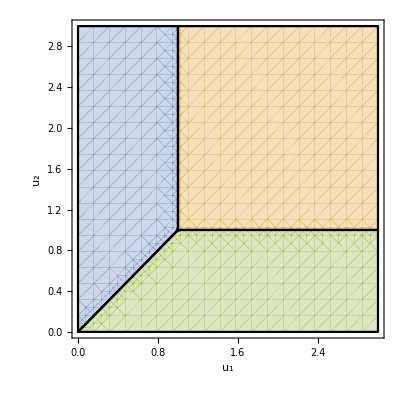

{1,1/10}

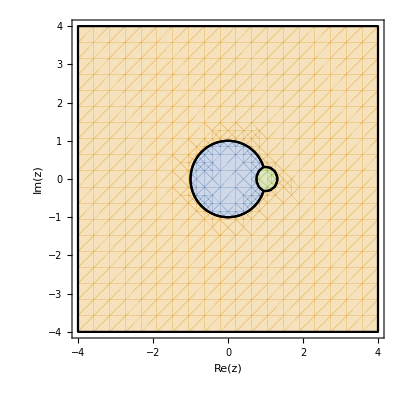

-Graphics-

```mathematica
Plot3D[If[1>A/B&&1>A,1,If[A>1&&A>A/B,2,If[A/B>1&&A/B>A,3]]],{A,0,3},{B,0,3},AxesLabel->Automatic]
RegionPlot[{1>Chop[A/B]&&1>Chop[A],Chop[A]>1&&Chop[A]>Chop[A/B],Chop[A/B]>1&&Chop[A/B]>Chop[A]},{A,0,3},{B,0,3},BoundaryStyle->Black,FrameLabel->{Text[Style["u_1",Black,FontSize->20]],Rotate[Text[Style["u_2",Black,FontSize->20]],-π/2]}]

z=x+ⅈ y;
zb=x-ⅈ y;
α=1/20 (19+ⅈ √39);
αb=Conjugate[%];
{α αb,(1-α)(1-αb)}//Simplify
A=(z zb)/(α αb)//Simplify;
B=((1-z) (1-zb))/((1-α)(1- αb))//Simplify;

RegionPlot[{1>Chop[A/B]&&1>Chop[A],Chop[A]>1&&Chop[A]>Chop[A/B],Chop[A/B]>1&&Chop[A/B]>Chop[A]},{x,-4,4},{y,-4,4},BoundaryStyle->Black,FrameLabel->{Text[Style["Re(z)",Black,FontSize->20]],Rotate[Text[Style["Im(z)",Black,FontSize->20]],-π/2]}]

ρ=x+ⅈ y;
ρb=x-ⅈ y;
z=(4ρ)/(1+ρ)^2;
zb=(4ρb)/(1+ρb)^2;
A=(z zb)/(α αb)//Simplify;
B=((1-z) (1-zb))/((1-α)(1- αb))//Simplify;

RegionPlot[{1>Chop[A/B]&&1>Chop[A]&&x^2+y^2<1,Chop[A]>1&&Chop[A]>Chop[A/B]&&x^2+y^2<1,Chop[A/B]>1&&Chop[A/B]>Chop[A]&&x^2+y^2<1},{x,-1,1},{y,-1,1},BoundaryStyle->Black,FrameLabel->{Text[Style["Re(ρ)",Black,FontSize->15]],Rotate[Text[Style["Im(ρ)",Black,FontSize->15]],-π/2]},MaxRecursion->10,PlotRange->{{-1,1},{-1,1}}]
(*Epilog->{Text[Style["I",Black,FontSize->20],{0.15,0.15}],Text[Style["II",Black,FontSize->20],{-0.5,0.4}],Text[Style["III",Black,FontSize->20],{0.7,0.3}]}*)

Clear[α,αb,z,zb,A,B,ρ,ρb]
```

-Graphics3D-

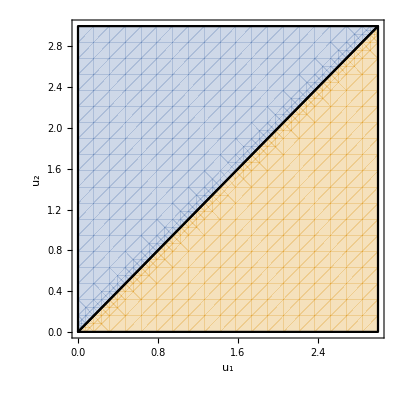

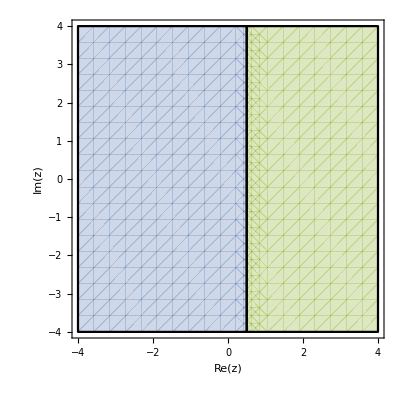

-Graphics-

```mathematica
Plot3D[If[1>A/B,1,If[False,2,If[A/B>1,3]]],{A,0,3},{B,0,3},AxesLabel->Automatic]
RegionPlot[{1>Chop[A/B],Chop[A/B]>1},{A,0,3},{B,0,3},BoundaryStyle->Black,FrameLabel->{Text[Style["u_1",Black,FontSize->20]],Rotate[Text[Style["u_2",Black,FontSize->20]],-π/2]}]

z=x+ⅈ y;
zb=x-ⅈ y;
A=z zb//Simplify;
B=(1-z) (1-zb)//Simplify;

RegionPlot[{1>Chop[A/B],False,Chop[A/B]>1},{x,-4,4},{y,-4,4},BoundaryStyle->Black,FrameLabel->{Text[Style["Re(z)",Black,FontSize->20]],Rotate[Text[Style["Im(z)",Black,FontSize->20]],-π/2]}]

ρ=x+ⅈ y;
ρb=x-ⅈ y;
z=(4ρ)/(1+ρ)^2;
zb=(4ρb)/(1+ρb)^2;
A=z zb//Simplify;
B=(1-z) (1-zb)//Simplify;
RegionPlot[{1>Chop[A/B]&&x^2+y^2<1,False,Chop[A/B]>1&&x^2+y^2<1},{x,-1,1},{y,-1,1},BoundaryStyle->Black,FrameLabel->{Text[Style["Re(ρ)",Black,FontSize->20]],Rotate[Text[Style["Im(ρ)",Black,FontSize->20]],-π/2]},MaxRecursion->10]

Clear[α,αb,z,zb,A,B,ρ,ρb]
```

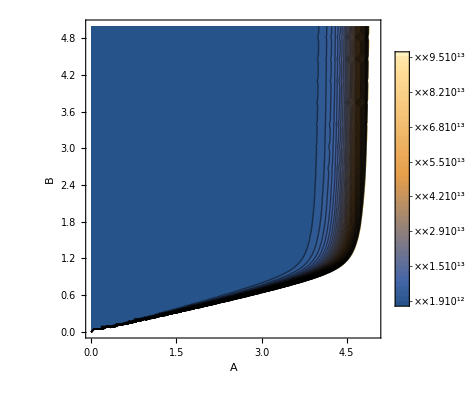

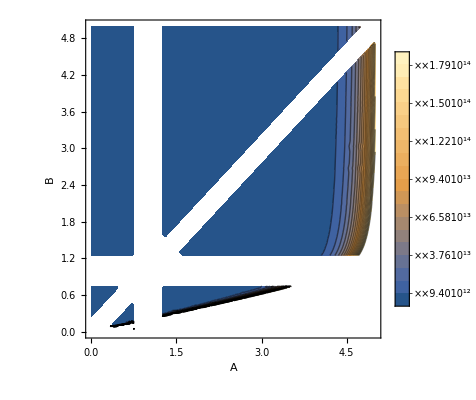

-Graphics-

```mathematica
NN=20;

1/(NN!)Sum[A^(NN-l12) B^(l12+l13-NN)((l12!l13!(NN-l12-l13)!)/((l13-numrl)!(NN-l12-l13-numpn)!(numrl-numkrl)!))^2 1/((-NN+2l12+numrl+numpn)!numkrl!(numpn-numrl+numkrl)!),{l12,0,NN},{l13,0,NN-l12},{numrl,0,l13},{numpn,Max[0,NN-2l12-numrl],NN-l12-l13},{numkrl,Max[0,numrl-numpn],numrl}]//.{N->NN};
ContourPlot[%,{A,0,5},{B,0,5},AxesLabel->Automatic,Contours->50,PlotLegends->Automatic]

ContourPlot[If[Abs[A-B]NN>5&&Abs[A-1]NN>5&&Abs[B-1]NN>5,B/((-1+A) (A-B))-(2 A^2 B)/((-1+A)^2 (A-B)^2 N)+(2 A^2 B (A+3 A^2+B+A B))/((-1+A)^3 (A-B)^3 N^2)+(-A/((A-B) (-1+B))-(2 (A B^2))/(((-1+B)^2 (-A+B)^2) N)+(2 A B^2 (A+B+A B+3 B^2))/((-1+B)^3 (-A+B)^3 N^2))(A/B)^N+((A B)/((-1+A) (-1+B))-(2 (A B))/(((-1+A)^2 (-1+B)^2) N)+(2 A B (3+A+B+A B))/((-1+A)^3 (-1+B)^3 N^2))A^N,NaN]//.{N->NN},{A,0,5},{B,0,5},AxesLabel->Automatic,Contours->50,PlotLegends->Automatic]

ContourPlot[If[Abs[A-B]NN>5&&Abs[A-1]NN>5&&Abs[B-1]NN>5,(B/((-1+A) (A-B))-(2 A^2 B)/((-1+A)^2 (A-B)^2 N)+(2 A^2 B (A+3 A^2+B+A B))/((-1+A)^3 (A-B)^3 N^2)+(-A/((A-B) (-1+B))-(2 (A B^2))/(((-1+B)^2 (-A+B)^2) N)+(2 A B^2 (A+B+A B+3 B^2))/((-1+B)^3 (-A+B)^3 N^2))(A/B)^N+((A B)/((-1+A) (-1+B))-(2 (A B))/(((-1+A)^2 (-1+B)^2) N)+(2 A B (3+A+B+A B))/((-1+A)^3 (-1+B)^3 N^2))A^N)/%%%,NaN]//.{N->NN},{A,0,5},{B,0,5},AxesLabel->Automatic,Contours->50,PlotLegends->Automatic]

Clear[NN]
```

```mathematica
(*NN=10;

1/(NN!)Sum[A^(NN-l12) B^(l12+l13-NN)((l12!l13!(NN-l12-l13)!)/((l13-numrl)!(NN-l12-l13-numpn)!(numrl-numkrl)!))^2 1/((-NN+2l12+numrl+numpn)!numkrl!(numpn-numrl+numkrl)!),{l12,0,NN},{l13,0,NN-l12},{numrl,0,l13},{numpn,Max[0,NN-2l12-numrl],NN-l12-l13},{numkrl,Max[0,numrl-numpn],numrl}]//.{A->z zb,B->(1-z)(1-zb),z->x+ⅈ y,zb->x-ⅈ y,N->NN};
ContourPlot[%,{x,0,4},{y,0,4},AxesLabel->Automatic,Contours->50,PlotLegends->Automatic]

ContourPlot[B/((-1+A) (A-B))-(2 A^2 B)/((-1+A)^2 (A-B)^2 N)+(2 A^2 B (A+3 A^2+B+A B))/((-1+A)^3 (A-B)^3 N^2)+(-A/((A-B) (-1+B))-(2 (A B^2))/(((-1+B)^2 (-A+B)^2) N)+(2 A B^2 (A+B+A B+3 B^2))/((-1+B)^3 (-A+B)^3 N^2))(A/B)^N+((A B)/((-1+A) (-1+B))-(2 (A B))/(((-1+A)^2 (-1+B)^2) N)+(2 A B (3+A+B+A B))/((-1+A)^3 (-1+B)^3 N^2))A^N//.{A->z zb,B->(1-z)(1-zb),z->x+ⅈ y,zb->x-ⅈ y,N->NN},{x,0,4},{y,0,4},AxesLabel->Automatic,Contours->50,PlotLegends->Automatic]

Clear[NN]
```

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian)(1 loop)_(non-conformal)e^-NS_eff

```mathematica
n=5;
```

```mathematica
(* 1-loop *)
```

```mathematica
(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]) (OSOXH/.{X[{x1,x2,x3,x4}]->0})/.{A->1,B->1,C->1}/.{Y[list_]:>YY[list],X[list_]:>XX[list],F[list_]:>FF[list]}//.{Log[ϵ^2/x[{i_,j_}]^2]:>2Log[ϵ]-2Log[x[{i,j}]],Log[(ϵ^2 x[{i_,j_}]^2)/(x[{k_,l_}]^2 x[{m_,n_}]^2)]:>2 Log[ϵ]+2 Log[x[{i,j}]]-2 Log[x[{k,l}]]-2 Log[x[{m,n}]],II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;

%/.{Subscript[ρhatinv, i_,j_]:>ρhatinv[i,j]}/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]/.(fieldRotationRnotOne/.Flatten[{{ρR[1,4]->ρR[1,3]}, {ρI[1,4]->ρI[1,3]}, {ρR[2,3]->ρR[2,4]}, {ρI[2,3]->ρI[2,4]}, {θ[3,4]->-θ[3,4]}}])/.fieldRotationRnotOne//PowerExpand//Distribute;

jacobianTimesOneLoop=List@@%;
%%==Total[%]

Monitor[
Table[jacobianTimesOneLoop[[i]]=Series[jacobianTimesOneLoop[[i]]/.{x__^n_:>Simplify[x]^n},{u,0,n-1}],{i,Length[jacobianTimesOneLoop]}],
Row[{ProgressIndicator[i,{1,Length[jacobianTimesOneLoop]}],i},""]];

jacobianTimesOneLoop=Total[jacobianTimesOneLoop];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify;
tmp=%/.(fieldRotationRnotOne/.Flatten[{{ρR[1,4]->ρR[1,3]}, {ρI[1,4]->ρI[1,3]}, {ρR[2,3]->ρR[2,4]}, {ρI[2,3]->ρI[2,4]}, {θ[3,4]->-θ[3,4]}}])/.fieldRotationRnotOne/.Log[x_]:>Log[x//Simplify]//PowerExpand//Simplify;

(* no linear term in action *)
SeriesCoefficient[tmp,{u,0,1}]==0
```

True

```mathematica
(* integrand *)
exponent=u^2 SeriesCoefficient[tmp,{u,0,2}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

fieldDepFactor=Table[0,{i,n}];
tmp2=jacobianTimesOneLoop(Series[(Exp[tmp-exponent-(tmp/.u->0)]//ExpandAll//Simplify//PowerExpand//Simplify),{u,0,n-1}]//PowerExpand);

Monitor[
Table[fieldDepFactor[[i]]=(SeriesCoefficient[tmp2,{u,0,i-1}]//Normal)/.u->1//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,Length[fieldDepFactor]}],
Row[{ProgressIndicator[i,{1,Length[fieldDepFactor]}],i},""]];

exponent=exponent/.u->1;

fieldDepFactor=Total[fieldDepFactor];

fieldIndepFactor=1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp/.u->0]/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}/.subzzbααb//PowerExpand)//ExpandAll//PowerExpand//Simplify//Distribute;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

(* simplify even powers *)
tmp2=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
Table[tmp2[[i]]=tmp2[[i]]//Simplify,{i,Length[tmp2]}],
Row[{ProgressIndicator[i,{1,Length[tmp2]}],i},""]];

fieldDepFactor=Total[tmp2];
```

True

```mathematica
(* integration *)
tmp3=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];
```

True

```mathematica
fieldIndepFactor Total[tmp3//PowerExpand//Collect[#,{Log[list_],Y[list_]},Simplify]&]//Collect[#,{Log[list_],Y[list_]},Simplify]&;
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];
Series[%,{N,∞,0}]
```

O[1/N]^1

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian)(1 loop)_conformal e^-NS_eff

```mathematica
n=7;
```

```mathematica
(* 1-loop *)
```

```mathematica
(g/(√2)+u r[1,2])(g/(√2)+u r[3,4])  (OSOXH-(OSOXH/.{X[{x1,x2,x3,x4}]->0}))/.{A->1,B->1,C->1}/.{II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;

%/.{Subscript[ρhatinv, i_,j_]:>ρhatinv[i,j]}/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]/.(fieldRotationRnotOne/.Flatten[{{ρR[1,4]->ρR[1,3]}, {ρI[1,4]->ρI[1,3]}, {ρR[2,3]->ρR[2,4]}, {ρI[2,3]->ρI[2,4]}, {θ[3,4]->-θ[3,4]}}])/.fieldRotationRnotOne//PowerExpand//Distribute;

jacobianTimesOneLoop=List@@%;
%%==Total[%]

Monitor[
Table[jacobianTimesOneLoop[[i]]=Series[jacobianTimesOneLoop[[i]]/.{x__^n_:>Simplify[x]^n},{u,0,n-1}],{i,Length[jacobianTimesOneLoop]}],
Row[{ProgressIndicator[i,{1,Length[jacobianTimesOneLoop]}],i},""]];

jacobianTimesOneLoop=Total[jacobianTimesOneLoop];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subzzbααb/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify;
tmp=%/.(fieldRotationRnotOne/.Flatten[{{ρR[1,4]->ρR[1,3]}, {ρI[1,4]->ρI[1,3]}, {ρR[2,3]->ρR[2,4]}, {ρI[2,3]->ρI[2,4]}, {θ[3,4]->-θ[3,4]}}])/.fieldRotationRnotOne/.Log[x_]:>Log[x//Simplify]//PowerExpand//Simplify;

(* no linear term in action *)
SeriesCoefficient[tmp,{u,0,1}]==0
```

True

```mathematica
(* integrand *)
exponent=u^2 SeriesCoefficient[tmp,{u,0,2}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

fieldDepFactor=Table[0,{i,n}];
tmp2=jacobianTimesOneLoop(Series[(Exp[tmp-exponent-(tmp/.u->0)]//ExpandAll//Simplify//PowerExpand//Simplify),{u,0,n-1}]//PowerExpand);

Monitor[
Table[fieldDepFactor[[i]]=(SeriesCoefficient[tmp2,{u,0,i-1}]//Normal)/.u->1//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,Length[fieldDepFactor]}],
Row[{ProgressIndicator[i,{1,Length[fieldDepFactor]}],i},""]];

exponent=exponent/.u->1;

fieldDepFactor=Total[fieldDepFactor];

fieldIndepFactor=1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp/.u->0]/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}/.subzzbααb//PowerExpand)//ExpandAll//PowerExpand//Simplify//Distribute;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

(* simplify even powers *)
tmp2=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
Table[tmp2[[i]]=tmp2[[i]]//Simplify,{i,Length[tmp2]}],
Row[{ProgressIndicator[i,{1,Length[tmp2]}],i},""]];

fieldDepFactor=Total[tmp2];
```

```mathematica
(* integration *)
tmp3=List@@fieldDepFactor;
Total[%]==fieldDepFactor

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];
```

True

```mathematica
fieldIndepFactor Total[tmp3//PowerExpand//Collect[#,{x[list_],Y[list_]},Simplify]&]//Collect[#,{x[list_],Y[list_]},Simplify]&;
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];
Series[%,{N,∞,3}]//Simplify

SeriesCoefficient[%,0]==-(2 g^2 α^2 αb^2 z zb(1-z)(1-zb)(z-α)(z-αb) (zb-α)(zb-αb))/((z zb-α αb)^2 (z zb (α+αb-1)-α αb(z+zb-1))^2)(((2π)^8 x[{x1,x3}]^2 x[{x2,x4}]^2)/π^2 X[{x1,x2,x3,x4}])/.Flatten[{{x[{x1,x2}]^2->(x[{x1,x3}]^2 x[{x2,x4}]^2)/x[{x3,x4}]^2 z zb}, {x[{x1,x4}]^2->(x[{x1,x3}]^2 x[{x2,x4}]^2)/x[{x2,x3}]^2(1-z)(1-zb)}, {zzboverααb->(z zb)/(α αb)}, {oneminuszoneminuszboveroneminusαoneminusαb->((1-z)(1-zb))/((1-α)(1-αb))}}]//Simplify

Series[(%%/.{zzboverααb->zzb/(α αb),oneminuszoneminuszboveroneminusαoneminusαb->oneminuszoneminuszb/((1-α)(1-αb))}//Simplify)/((λ(N+1))/(8 π^2 N^2)(rr(N(rr-1)+rr+1))/(1-rr)^3(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))((2π)^8 x[{x1,x3}]^2 x[{x2,x4}]^2)/π^2 X[{x1,x2,x3,x4}]/.{λ->16 π^2 g^2}/.{rr->zzb/oneminuszoneminuszb}//Simplify)/.{α->inf α,αb->inf αb},{inf,∞,0}]
```

-1/((oneminuszoneminuszboveroneminusαoneminusαb-zzboverααb)^2 (-1+zzboverααb)^2)512 (g^2 π^6 ((-1+oneminuszoneminuszboveroneminusαoneminusαb) (oneminuszoneminuszboveroneminusαoneminusαb-zzboverααb) zzboverααb x[{x1,x4}]^2 x[{x2,x3}]^2+oneminuszoneminuszboveroneminusαoneminusαb (-1+zzboverααb) ((-1+oneminuszoneminuszboveroneminusαoneminusαb) zzboverααb x[{x1,x3}]^2 x[{x2,x4}]^2+(-oneminuszoneminuszboveroneminusαoneminusαb+zzboverααb) x[{x1,x2}]^2 x[{x3,x4}]^2)) X[{x1,x2,x3,x4}])+√O[1/N]

True

(1+O[1/inf]^1)+√O[1/N]

```mathematica
(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))==1/.{rr->zzb/oneminuszoneminuszb}/.{zzb->(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2),oneminuszoneminuszb->(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)}//Simplify
```

True

## NLO: [1512.02926] vs here

```mathematica
-(2 g^2 α^2 αb^2 z zb(1-z)(1-zb)(z-α)(z-αb) (zb-α)(zb-αb))/((z zb-α αb)^2 (z zb (α+αb-1)-α αb(z+zb-1))^2)(((2π)^8 x[{x1,x3}]^2 x[{x2,x4}]^2)/π^2 X[{x1,x2,x3,x4}]);
tmp0=%+(((z zb)/(α αb))/(((1-z)(1- zb))/((1-α)(1-αb))))^N(%/.Flatten[{{z->1-z}, {zb->1-zb}, {α->1-α}, {αb->1-αb}, {x2->x4}, {x4->x2}}])+((z zb)/(α αb))^N(%/.Flatten[{{z->1/z}, {zb->1/zb}, {α->1/α}, {αb->1/αb}, {x2->x3}, {x3->x2}}])/.sub1/.{x[list_]:>x[list//Sort]}/.{x[{xx_,yy__}]^2:>Subscript[u, (xx/.{x1->X1,x2->X2,x3->X3,x4->X4})(yy/.{x1->X1,x2->X2,x3->X3,x4->X4})]/sqrtd[xx/.{x1->1,x2->2,x3->3,x4->4},yy/.{x1->1,x2->2,x3->3,x4->4}]^2}/.{g^2->λ/(16 π^2)}/.subzzbααb//Simplify//PowerExpand//Simplify
```

-((32 π^4 (-1+z) (-1+zb) (z-α) (zb-α) (z-αb) (zb-αb) λ ((-1+z)^-N z^(1+N) (-1+zb)^-N zb^(1+N) (-1+α)^(2+N) α^-N (-1+αb)^(2+N) αb^-N (z zb-α αb)^2 u_(X1 X3) u_(X2 X4)+z zb α^2 αb^2 (z (-1+zb)-zb+α+αb-α αb)^2 u_(X1 X3) u_(X2 X4)+z^N zb^N zzboverααb α^-N αb^-N (z α αb+(-1+zb) α αb-z zb (-1+α+αb))^2 u_(X1 X2) u_(X3 X4)) X[{x1,x2,x3,x4}])/((z zb-α αb)^2 (z (-1+zb)-zb+α+αb-α αb)^2 (z α αb+(-1+zb) α αb-z zb (-1+α+αb))^2 sqrtd[1,3]^2 sqrtd[2,4]^2))

```mathematica
(* k=2,3,N *)
k=N;

(* ((λ/N)^(2k) (2.11))/(2-pt)^2 *)
(λ/N)^(2k)(λ/(4 π^2)(1/2(N/2)^(2k-2)k^4/((4 π^2)^(2k)))(d[1,2]^2 d[3,4]^2 x[{x1,x2}]^2 x[{x3,x4}]^2+d[1,3]^2 d[2,4]^2 x[{x1,x3}]^2 x[{x2,x4}]^2+d[1,4]^2 d[2,3]^2 x[{x1,x4}]^2 x[{x2,x3}]^2+d[1,2]d[2,3]d[3,4]d[1,4](x[{x1,x3}]^2 x[{x2,x4}]^2-x[{x1,x2}]^2 x[{x3,x4}]^2-x[{x1,x4}]^2 x[{x2,x3}]^2)+d[1,2]d[1,3]d[2,4]d[3,4](x[{x1,x4}]^2 x[{x2,x3}]^2-x[{x1,x2}]^2 x[{x3,x4}]^2-x[{x1,x3}]^2 x[{x2,x4}]^2)+d[1,3]d[1,4]d[2,3]d[2,4](x[{x1,x2}]^2 x[{x3,x4}]^2-x[{x1,x4}]^2 x[{x2,x3}]^2-x[{x1,x3}]^2 x[{x2,x4}]^2))Sum[d[1,2]^b12 d[1,3]^b13 d[1,4]^(k-2-b12-b13)d[2,3]^(k-2-b12-b13)d[2,4]^b13 d[3,4]^b12,{b12,0,k-2},{b13,0,k-2-b12}](-((4 π^2)^4)/(4 π^2)X[{x1,x2,x3,x4}]))/Switch[k,N,N!(λ/(8 π^2)d[1,2])^N N!(λ/(8 π^2)d[3,4])^N,_,k(λ/(8 π^2)d[1,2])^k k(λ/(8 π^2)d[3,4])^k];
tmp1=%/.{d[x_,y_]:>sqrtd[x,y]^2}/.{x[{xx_,yy__}]^2:>Subscript[u, (xx/.{x1->X1,x2->X2,x3->X3,x4->X4})(yy/.{x1->X1,x2->X2,x3->X3,x4->X4})]/sqrtd[xx/.{x1->1,x2->2,x3->3,x4->4},yy/.{x1->1,x2->2,x3->3,x4->4}]^2}/.subzzbααb/.Flatten[{{zzboverααb->(z zb)/(α αb)}, {oneminuszoneminuszboveroneminusαoneminusαb->((1-z)(1-zb))/((1-α)(1-αb))}}]//PowerExpand//Simplify

(* here *)
Switch[k,2,1/N^2 2 λ^5 (-(II[{x1,x2}] II[{x1,x3}] II[{x2,x4}] II[{x3,x4}] Subscript[u, X1 X2] Subscript[u, X1 X3] Subscript[u, X2 X4] Subscript[u, X3 X4])/(II[{x1,x4}] II[{x2,x3}])+II[{x1,x2}] II[{x3,x4}] Subscript[u, X1 X2] Subscript[u, X3 X4] (Subscript[u, X2 X3] Subscript[u, X1 X4]+Subscript[u, X1 X3] Subscript[u, X2 X4]-Subscript[u, X1 X2] Subscript[u, X3 X4])+II[{x1,x3}] II[{x2,x4}] Subscript[u, X1 X3] Subscript[u, X2 X4] (Subscript[u, X2 X3] Subscript[u, X1 X4]-Subscript[u, X1 X3] Subscript[u, X2 X4]+Subscript[u, X1 X2] Subscript[u, X3 X4])-(II[{x1,x4}] II[{x2,x3}] Subscript[u, X2 X3] Subscript[u, X1 X4] (II[{x1,x3}]^2 II[{x2,x4}]^2 Subscript[u, X1 X3] Subscript[u, X2 X4]+II[{x1,x2}]^2 II[{x3,x4}]^2 Subscript[u, X1 X2] Subscript[u, X3 X4]+II[{x1,x2}] II[{x1,x3}] II[{x2,x4}] II[{x3,x4}] (Subscript[u, X2 X3] Subscript[u, X1 X4]-Subscript[u, X1 X3] Subscript[u, X2 X4]-Subscript[u, X1 X2] Subscript[u, X3 X4])))/(II[{x1,x2}] II[{x1,x3}] II[{x2,x4}] II[{x3,x4}])) X[{x1,x2,x3,x4}]/Switch[k,N,N!(λ/(8 π^2)d[1,2])^N N!(λ/(8 π^2)d[3,4])^N,_,k(λ/(8 π^2)d[1,2])^k k(λ/(8 π^2)d[3,4])^k],3,-((81 λ^7 (II[{x1,x3}]^2 II[{x1,x4}]^2 II[{x2,x3}]^2 II[{x2,x4}]^2 Subscript[u, X1 X3] Subscript[u, X2 X3] Subscript[u, X1 X4] Subscript[u, X2 X4] (II[{x1,x4}] II[{x2,x3}] Subscript[u, X2 X3] Subscript[u, X1 X4]+II[{x1,x3}] II[{x2,x4}] Subscript[u, X1 X3] Subscript[u, X2 X4])+II[{x1,x2}]^2 II[{x3,x4}]^2 Subscript[u, X1 X2] (II[{x1,x4}]^3 II[{x2,x3}]^3 Subscript[u, X2 X3]^2 Subscript[u, X1 X4]^2-II[{x1,x3}] II[{x1,x4}]^2 II[{x2,x3}]^2 II[{x2,x4}] Subscript[u, X1 X3] Subscript[u, X2 X3] Subscript[u, X1 X4] Subscript[u, X2 X4]-II[{x1,x3}]^2 II[{x1,x4}] II[{x2,x3}] II[{x2,x4}]^2 Subscript[u, X1 X3] Subscript[u, X2 X3] Subscript[u, X1 X4] Subscript[u, X2 X4]+II[{x1,x3}]^3 II[{x2,x4}]^3 Subscript[u, X1 X3]^2 Subscript[u, X2 X4]^2) Subscript[u, X3 X4]+II[{x1,x2}]^3 II[{x3,x4}]^3 Subscript[u, X1 X2]^2 Subscript[u, X3 X4]^2 (II[{x1,x4}]^2 II[{x2,x3}]^2 Subscript[u, X2 X3] Subscript[u, X1 X4]+II[{x1,x3}]^2 II[{x2,x4}]^2 Subscript[u, X1 X3] Subscript[u, X2 X4]-II[{x1,x3}] II[{x1,x4}] II[{x2,x3}] II[{x2,x4}] (Subscript[u, X2 X3] Subscript[u, X1 X4]+Subscript[u, X1 X3] Subscript[u, X2 X4]-Subscript[u, X1 X2] Subscript[u, X3 X4]))-II[{x1,x2}] II[{x1,x3}] II[{x1,x4}] II[{x2,x3}] II[{x2,x4}] II[{x3,x4}] (II[{x1,x3}] II[{x1,x4}] II[{x2,x3}] II[{x2,x4}] Subscript[u, X1 X2] Subscript[u, X1 X3] Subscript[u, X2 X3] Subscript[u, X1 X4] Subscript[u, X2 X4] Subscript[u, X3 X4]+II[{x1,x3}]^2 II[{x2,x4}]^2 Subscript[u, X1 X3]^2 Subscript[u, X2 X4]^2 (Subscript[u, X2 X3] Subscript[u, X1 X4]-Subscript[u, X1 X3] Subscript[u, X2 X4]+Subscript[u, X1 X2] Subscript[u, X3 X4])+II[{x1,x4}]^2 II[{x2,x3}]^2 Subscript[u, X2 X3]^2 Subscript[u, X1 X4]^2 (-Subscript[u, X2 X3] Subscript[u, X1 X4]+Subscript[u, X1 X3] Subscript[u, X2 X4]+Subscript[u, X1 X2] Subscript[u, X3 X4]))) X[{x1,x2,x3,x4}])/(32 N^2 II[{x1,x2}] II[{x1,x3}] II[{x1,x4}] II[{x2,x3}] II[{x2,x4}] II[{x3,x4}]))/Switch[k,N,N!(λ/(8 π^2)d[1,2])^N N!(λ/(8 π^2)d[3,4])^N,_,k(λ/(8 π^2)d[1,2])^k k(λ/(8 π^2)d[3,4])^k],N,tmp0];
tmp2=%/.{d[x_,y_]:>sqrtd[x,y]^2}/.{II[{xx_,yy_}]:>1/(4 π^2)sqrtd[xx/.{x1->1,x2->2,x3->3,x4->4},yy/.{x1->1,x2->2,x3->3,x4->4}]^2/Subscript[u, (xx/.{x1->X1,x2->X2,x3->X3,x4->X4})(yy/.{x1->X1,x2->X2,x3->X3,x4->X4})]}/.subzzbααb/.Flatten[{{zzboverααb->(z zb)/(α αb)}, {oneminuszoneminuszboveroneminusαoneminusαb->((1-z)(1-zb))/((1-α)(1-αb))}}]//PowerExpand//Simplify

Clear[k]
```

(32 N^2 π^4 (-1+z)^2 z^(2+N) (-1+zb)^2 zb^(2+N) α^-N αb^-N (-(1-z)^-N (1-zb)^-N (1-α)^N (1-αb)^N+((-1+α) (-1+αb))/((-1+z) (-1+zb))-(α αb)/(z zb)+((1-z)^-N (1-zb)^-N (1-α)^N α (1-αb)^N αb)/(z zb)+z^-N zb^-N α^N αb^N-(z^-N zb^-N (-1+α) α^N (-1+αb) αb^N)/((-1+z) (-1+zb))) λ (-u_(X2 X3) u_(X1 X4)+((-1+α) (-1+αb) u_(X2 X3) u_(X1 X4))/((-1+z) (-1+zb))-(α αb u_(X2 X3) u_(X1 X4))/(z zb)+((-1+z) (-1+zb) α αb u_(X2 X3) u_(X1 X4))/(z zb (-1+α) (-1+αb))+u_(X1 X3) u_(X2 X4)-((-1+α) (-1+αb) u_(X1 X3) u_(X2 X4))/((-1+z) (-1+zb))-(α αb u_(X1 X3) u_(X2 X4))/(z zb)+((-1+α) α (-1+αb) αb u_(X1 X3) u_(X2 X4))/((-1+z) z (-1+zb) zb)-u_(X1 X2) u_(X3 X4)-((-1+α) (-1+αb) u_(X1 X2) u_(X3 X4))/((-1+z) (-1+zb))+(z zb (-1+α) (-1+αb) u_(X1 X2) u_(X3 X4))/((-1+z) (-1+zb) α αb)+(α αb u_(X1 X2) u_(X3 X4))/(z zb)) X[{x1,x2,x3,x4}])/((z zb-α αb) (z (-1+zb)-zb+α+αb-α αb) (-z α αb-(-1+zb) α αb+z zb (-1+α+αb)) (N!)^2 sqrtd[1,3]^2 sqrtd[2,4]^2)

-((32 π^4 (-1+z) z (-1+zb) zb (z-α) (zb-α) (z-αb) (zb-αb) λ (α^2 αb^2 (z (-1+zb)-zb+α+αb-α αb)^2 u_(X1 X3) u_(X2 X4)+(-1+z)^-N z^N (-1+zb)^-N zb^N (-1+α)^(2+N) α^-N (-1+αb)^(2+N) αb^-N (-z zb+α αb)^2 u_(X1 X3) u_(X2 X4)+z^N zb^N α^(-1-N) αb^(-1-N) (z α αb+(-1+zb) α αb-z zb (-1+α+αb))^2 u_(X1 X2) u_(X3 X4)) X[{x1,x2,x3,x4}])/((z zb-α αb)^2 (z (-1+zb)-zb+α+αb-α αb)^2 (z α αb+(-1+zb) α αb-z zb (-1+α+αb))^2 sqrtd[1,3]^2 sqrtd[2,4]^2))

```mathematica
(* compare *)
Series[tmp1/tmp2/.Flatten[{{zb->Conjugate[z]}, {αb->Conjugate[α]}}]/.Flatten[{{z->(3+4 ⅈ)/10}, {α->(2+5 ⅈ)/10}}]//Simplify,{N,∞,0}]//Simplify//Normal//FullSimplify
```

# Simplest 4-pt

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ e^-NS_eff

```mathematica
(* integrand *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr//Simplify//PowerExpand//Simplify;

1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}/.subr//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp]//ExpandAll//Simplify;

Integrate[%,{ρR[1,3],-∞,∞},{ρI[1,3],-∞,∞},{ρR[2,4],-∞,∞},{ρI[2,4],-∞,∞},Assumptions->g>0 && N>0];

1/(π^4 (N!)^2)4^(2+N) ⅇ^(-(2 N (ρI[1,2]^2+ρI[1,4]^2+ρI[2,3]^2+ρI[3,4]^2+ρR[1,2]^2+ρR[1,4]^2+ρR[2,3]^2+ρR[3,4]^2))/g^2) g^(-4 (2+N)) N^(4+2 N) Sum[Binomial[N,n1]Binomial[N,n2] ((ρI[1,2]-ⅈ ρR[1,2])(ρI[3,4]-ⅈ ρR[3,4]))^n1(√rr (ρI[1,4]-ⅈ ρR[1,4]) (ρI[2,3]+ⅈ ρR[2,3]))^(N-n1)((ρI[1,2]+ⅈ ρR[1,2]) (ρI[3,4]+ⅈ ρR[3,4]))^n2(√rr (ρI[1,4]+ⅈ ρR[1,4]) (ρI[2,3]-ⅈ ρR[2,3]))^(N-n2),{n1,0,N},{n2,0,N}]/%==1//FullSimplify
```

True

```mathematica
(* complex Gaussian integral *)
```

```mathematica
Table[Integrate[ⅇ^(-a z zb) z^n1 zb^n2/.{z->x+ⅈ y,zb->x-ⅈ y}//Simplify//Expand,{x,-∞,∞},{y,-∞,∞},Assumptions->a>0]==π/a^(n1+1) n1! n1,n2,{n1,0,6},{n2,0,6}]//Flatten//Union
```

$Aborted

```mathematica
(* integration *)

1/(π^4 (N!)^2)4^(2+N) ⅇ^(-(2 N (ρI[1,2]^2+ρI[1,4]^2+ρI[2,3]^2+ρI[3,4]^2+ρR[1,2]^2+ρR[1,4]^2+ρR[2,3]^2+ρR[3,4]^2))/g^2) g^(-4 (2+N)) N^(4+2 N) Binomial[N,n1]Binomial[N,n2] ((ρI[1,2]-ⅈ ρR[1,2])(ρI[3,4]-ⅈ ρR[3,4]))^n1(√rr (ρI[1,4]-ⅈ ρR[1,4]) (ρI[2,3]+ⅈ ρR[2,3]))^(N-n1)((ρI[1,2]+ⅈ ρR[1,2]) (ρI[3,4]+ⅈ ρR[3,4]))^n2(√rr (ρI[1,4]+ⅈ ρR[1,4]) (ρI[2,3]-ⅈ ρR[2,3]))^(N-n2)/.{ρR[i_,j_]:>(ρρ[i,j]+ρρ[j,i])/2,ρI[i_,j_]:>(ρρ[i,j]-ρρ[j,i])/(2ⅈ)}//Simplify//PowerExpand//Simplify;
```

```mathematica
1/(π^4 (N!)^2)(-1)^(n1+n2) 4^(2+N)  g^(-4 (2+N)) N^(4+2 N) rr^(N-n1/2-n2/2) Binomial[N,n1] Binomial[N,n2](π/(((2N)/g^2)^((n1+n2)/2+1)) n1! n1,n2 π/(((2N)/g^2)^((N-n1+N-n2)/2+1)) (N-n1)! n1,n2)^2/.n2->n1//Simplify//FullSimplify//PowerExpand;
Sum[%/.{(-1)^(2 n1) ->1},{n1,0,N}]
```

(-1+rr^(1+N))/(-1+rr)

## Saddle-pt of ∫dρ e^(-NS_eff+log(r_12 r_34))

```mathematica
(* find saddle-pt in Cartesian fields *)
```

```mathematica
Table[(1-i,j)(ρρ[i,j]-g^2/2 sqrtd[i,j] Inverse[Table[sqrtd[l,m] (1-l,m)ρρ[l,m],{l,4},{m,4}]][[i,j]])==0,{i,4},{j,4}]//.sub/.simplest4pt//Simplify//Flatten;
Solve[%,Table[ρρ[i,j],{i,4},{j,4}]//Flatten]//MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(ρρ[1,2]→0 | ρρ[1,3]→0 | ρρ[2,1]→0 | ρρ[2,3]→g^2/(2 ρρ[3,2]) | ρρ[2,4]→0 | ρρ[3,1]→0 | ρρ[3,4]→0 | ρρ[4,1]→g^2/(2 ρρ[1,4]) | ρρ[4,2]→0 | ρρ[4,3]→0
ρρ[1,3]→0 | ρρ[1,4]→0 | ρρ[2,1]→g^2/(2 ρρ[1,2]) | ρρ[2,3]→0 | ρρ[2,4]→0 | ρρ[3,1]→0 | ρρ[3,2]→0 | ρρ[4,1]→0 | ρρ[4,2]→0 | ρρ[4,3]→g^2/(2 ρρ[3,4]))

```mathematica
(* find saddle-pt in Cartesian+polar fields *)
```

```mathematica
tmp=N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]+1/2 Log[ρR[1,2]^2+ρI[1,2]^2]+1/2 Log[ρR[3,4]^2+ρI[3,4]^2]/.sub/.simplest4pt/.Flatten[{{ρR[1,2]->r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->r[3,4]Sin[θ[3,4]]}}]//Simplify//Collect[#,Log[x__]]&;
Table[D[tmp,VariablesRnotOne[[i]]]==0,{i,Length[VariablesRnotOne]}]/.Flatten[{{r[1,2]->g/(√2) √(1+1/(2N))}, {r[3,4]->g/(√2)√(1+1/(2N))}, {ρI[i_,j_]:>0}, {ρR[i_,j_]:>0}}]//Simplify//Union
```

{True}

## Continue: r=1

```mathematica
(* find saddle-pt in Cartesian fields *)
```

```mathematica
Clear[nn]

Table[(1-i,j)(ρρ[i,j]-g^2/2 sqrtd[i,j] Inverse[Table[sqrtd[l,m] (1-l,m)ρρ[l,m],{l,4},{m,4}]][[i,j]])==0,{i,4},{j,4}]//.sub/.simplest4pt/.subr/.rr->1//PowerExpand//Simplify//Flatten;
tmp=Solve[%,Table[ρρ[i,j],{i,4},{j,4}]//Flatten];
tmp//MatrixForm

Table[tmp[[1,i,1]]==tmp[[1,i,2]],{i,Length[tmp[[1]]]}]/.Flatten[{{ρρ[1,2]->R[1,2] Exp[ⅈ θ[1,2]]}, {ρρ[2,1]->R[1,2] Exp[-ⅈ θ[1,2]]}, {ρρ[3,4]->R[1,2] Exp[ⅈ θ[3,4]]}, {ρρ[4,3]->R[1,2] Exp[-ⅈ θ[3,4]]}, {ρρ[2,3]->-√(g^2/2-R[1,2]^2)ⅇ^(ⅈ (θ[1,4]-θ[1,2]-θ[3,4]))}, {ρρ[3,2]->-√(g^2/2-R[1,2]^2)ⅇ^(-ⅈ (θ[1,4]-θ[1,2]-θ[3,4]))}, {ρρ[1,4]->√(g^2/2-R[1,2]^2) Exp[ⅈ θ[1,4]]}, {ρρ[4,1]->√(g^2/2-R[1,2]^2) Exp[-ⅈ θ[1,4]]}, {ρρ[1,3]->0}, {ρρ[3,1]->0}, {ρρ[2,4]->0}, {ρρ[4,2]->0}}]//Simplify//Union
Table[tmp[[1,i,1]]==tmp[[1,i,2]],{i,Length[tmp[[1]]]}]/.Flatten[{{ρρ[1,3]->0}, {ρρ[3,1]->0}, {ρρ[2,4]->0}, {ρρ[4,2]->0}}]/.{ρρ[i_,j_]:>ρ[i,j]}/.Flatten[{{ρR[1,2]->r Cos[α/2]Cos[θ1/2]Cos[1/4(2φ1+χ+ξ)]}, {ρI[1,2]->r Cos[α/2]Cos[θ1/2]Sin[1/4(2φ1+χ+ξ)]}, {ρR[3,4]->r Cos[α/2]Sin[θ1/2]Cos[1/4(-2φ1+χ+ξ)]}, {ρI[3,4]->r Cos[α/2]Sin[θ1/2]Sin[1/4(-2φ1+χ+ξ)]}, {ρR[2,3]->r Sin[α/2]Cos[θ2/2]Cos[1/4(2φ2-χ+ξ)]}, {ρI[2,3]->r Sin[α/2]Cos[θ2/2]Sin[1/4(2φ2-χ+ξ)]}, {ρR[1,4]->r Sin[α/2]Sin[θ2/2]Cos[-1/4(-2φ2-χ+ξ)]}, {ρI[1,4]->r Sin[α/2]Sin[θ2/2]Sin[-1/4(-2φ2-χ+ξ)]}}]/.Flatten[{{r->g}, {θ1->π/2}, {θ2->π/2}, {ξ->(2 nn+1)π}}]//Simplify//Union//Table[#,{nn,0,3}]&//Flatten//Union

Table[tmp[[2,i,1]]==tmp[[2,i,2]],{i,Length[tmp[[1]]]}]/.Flatten[{{ρρ[1,2]->R[1,2] Exp[ⅈ θ[1,2]]}, {ρρ[2,1]->R[1,2] Exp[-ⅈ θ[1,2]]}, {ρρ[3,4]->R[1,2] Exp[ⅈ θ[3,4]]}, {ρρ[4,3]->R[1,2] Exp[-ⅈ θ[3,4]]}, {ρρ[2,3]->√(g^2/2-R[1,2]^2)ⅇ^(ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[3,2]->√(g^2/2-R[1,2]^2)ⅇ^(-ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[1,4]->√(g^2/2-R[1,2]^2) Exp[ⅈ θ[1,4]]}, {ρρ[4,1]->√(g^2/2-R[1,2]^2) Exp[-ⅈ θ[1,4]]}, {ρρ[1,3]->0}, {ρρ[3,1]->0}, {ρρ[2,4]->0}, {ρρ[4,2]->0}}]/.{R[1,2]->g/(√2)}//Simplify//Union
Table[tmp[[3,i,1]]==tmp[[3,i,2]],{i,Length[tmp[[1]]]}]/.Flatten[{{ρρ[1,2]->R[1,2] Exp[ⅈ θ[1,2]]}, {ρρ[2,1]->R[1,2] Exp[-ⅈ θ[1,2]]}, {ρρ[3,4]->R[1,2] Exp[ⅈ θ[3,4]]}, {ρρ[4,3]->R[1,2] Exp[-ⅈ θ[3,4]]}, {ρρ[2,3]->√(g^2/2-R[1,2]^2)ⅇ^(ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[3,2]->√(g^2/2-R[1,2]^2)ⅇ^(-ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[1,4]->√(g^2/2-R[1,2]^2) Exp[ⅈ θ[1,4]]}, {ρρ[4,1]->√(g^2/2-R[1,2]^2) Exp[-ⅈ θ[1,4]]}, {ρρ[1,3]->0}, {ρρ[3,1]->0}, {ρρ[2,4]->0}, {ρρ[4,2]->0}}]/.{R[1,2]->0}//Simplify//Union
Table[tmp[[4,i,1]]==tmp[[4,i,2]],{i,Length[tmp[[1]]]}]/.Flatten[{{ρρ[1,2]->R[1,2] Exp[ⅈ θ[1,2]]}, {ρρ[2,1]->R[1,2] Exp[-ⅈ θ[1,2]]}, {ρρ[3,4]->R[1,2] Exp[ⅈ θ[3,4]]}, {ρρ[4,3]->R[1,2] Exp[-ⅈ θ[3,4]]}, {ρρ[2,3]->√(g^2/2-R[1,2]^2)ⅇ^(ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[3,2]->√(g^2/2-R[1,2]^2)ⅇ^(-ⅈ (θ[1,4]-θ[1,2]-θ[3,4]+π))}, {ρρ[1,4]->√(g^2/2-R[1,2]^2) Exp[ⅈ θ[1,4]]}, {ρρ[4,1]->√(g^2/2-R[1,2]^2) Exp[-ⅈ θ[1,4]]}, {ρρ[1,3]->0}, {ρρ[3,1]->0}, {ρρ[2,4]->0}, {ρρ[4,2]->0}}]/.{R[1,2]->0}//Simplify//Union
```

Solve::svars: Equations may not give solutions for all "solve" variables.

({ρρ[1,2]→(g^2-2 ρρ[1,4] ρρ[4,1])/(2 ρρ[2,1]),ρρ[1,3]→0,ρρ[2,3]→(2 ρρ[1,4] ρρ[2,1] ρρ[4,3])/(-g^2+2 ρρ[1,4] ρρ[4,1]),ρρ[2,4]→0,ρρ[3,1]→0,ρρ[3,2]→(-g^2 ρρ[4,1]+2 ρρ[1,4] ρρ[4,1]^2)/(2 ρρ[2,1] ρρ[4,3]),ρρ[3,4]→(g^2-2 ρρ[1,4] ρρ[4,1])/(2 ρρ[4,3]),ρρ[4,2]→0}
{ρρ[1,2]→g^2/(2 ρρ[2,1]),ρρ[1,3]→0,ρρ[1,4]→0,ρρ[2,3]→0,ρρ[2,4]→0,ρρ[3,1]→0,ρρ[3,2]→-(g^2 ρρ[4,1])/(2 ρρ[2,1] ρρ[4,3]),ρρ[3,4]→g^2/(2 ρρ[4,3]),ρρ[4,2]→0}
{ρρ[1,2]→-(g^2 ρρ[4,3])/(2 ρρ[2,3] ρρ[4,1]),ρρ[1,3]→0,ρρ[1,4]→g^2/(2 ρρ[4,1]),ρρ[2,1]→0,ρρ[2,4]→0,ρρ[3,1]→0,ρρ[3,2]→g^2/(2 ρρ[2,3]),ρρ[3,4]→0,ρρ[4,2]→0}
{ρρ[1,2]→0,ρρ[1,3]→0,ρρ[1,4]→g^2/(2 ρρ[4,1]),ρρ[2,4]→0,ρρ[3,1]→0,ρρ[3,2]→g^2/(2 ρρ[2,3]),ρρ[3,4]→-(g^2 ρρ[2,1])/(2 ρρ[2,3] ρρ[4,1]),ρρ[4,2]→0,ρρ[4,3]→0})

{True}

{True}

{True}

«2 more identical outputs»

```mathematica
(* on the saddle-pt *)
```

```mathematica
Solve[{1/4(2φ1+χ+ξ)==θ[1,2],1/4(-2φ1+χ+ξ)==θ[3,4],1/4(2φ2-χ+ξ)==θ[1,4]-θ[1,2]-θ[3,4]+(2 nn+1)π,1/4(-2φ2-χ+ξ)==-θ[1,4]},{φ1,φ2,χ,ξ}]//Transpose//MatrixForm
```

(φ1→θ[1,2]-θ[3,4]
φ2→π+2 nn π-θ[1,2]+2 θ[1,4]-θ[3,4]
χ→-π-2 nn π+2 θ[1,2]+2 θ[3,4]
ξ→π+2 nn π)

```mathematica
Clear[nn]

(* change of coordinates *)
tmp=Flatten[{{r Cos[α/2]Cos[θ1/2]Exp[ⅈ/4(+2φ1+χ+ξ)]}, {r Cos[α/2]Sin[θ1/2]Exp[ⅈ/4(-2φ1+χ+ξ)]}, {r Sin[α/2]Cos[θ2/2]Exp[ⅈ/4(+2φ2-χ+ξ)]}, {r Sin[α/2]Sin[θ2/2]Exp[ⅈ/4(-2φ2-χ+ξ)]}}];
tmp2={r,α,θ1,θ2,φ1,φ2,χ,ξ};
tmp3={dr,dα,dθ1,dθ2,dφ1,dφ2,dχ,dξ};

(* line element on R^8 *)
Sum[D[tmp,tmp2[[i]]]tmp3[[i]],{i,Length[tmp2]}]//Simplify;
ds2=%.Conjugate[%]//Expand//ComplexExpand//Simplify//Expand//CoefficientRules[#,tmp3]&//Simplify//FromCoefficientRules[#,tmp3]&;
ds2==Total[Sum[D[Re[tmp]//ComplexExpand,tmp2[[i]]]tmp3[[i]],{i,Length[tmp2]}]^2]+Total[Sum[D[Im[tmp]//ComplexExpand,tmp2[[i]]]tmp3[[i]],{i,Length[tmp2]}]^2]//Expand//ComplexExpand//Simplify//Expand//CoefficientRules[#,tmp3]&//Simplify//FromCoefficientRules[#,tmp3]&//Simplify
ds2==dr^2+r^2(1/4(dα^2+Cos[α/2]^2(dθ1^2+Sin[θ1]^2 dφ1^2)+Sin[α/2]^2(dθ2^2+Sin[θ2]^2 dφ2^2)+Sin[α/2]^2 Cos[α/2]^2(dχ+Cos[θ1]dφ1-Cos[θ2]dφ2)^2)+1/16(dξ+Cos[α]dχ+2 Cos[α/2]^2 Cos[θ1]dφ1+2 Sin[α/2]^2 Cos[θ2]dφ2)^2)//Simplify

(* metric on R^8 *)
G=Coefficient[ds2//ExpandAll,KroneckerProduct[tmp3,tmp3]]//Simplify;
G=DiagonalMatrix[Diagonal[G]]+(G-DiagonalMatrix[Diagonal[G]])/2;
ds2==tmp3.G.tmp3//Simplify

(* Jacobian *)
tmp4=0 IdentityMatrix[8];
tmp4[[1;;4,1;;8]]=Table[D[Re[tmp[[i]]]//ComplexExpand,tmp2[[j]]],{i,4},{j,8}];
tmp4[[5;;8,1;;8]]=Table[D[Im[tmp[[i]]]//ComplexExpand,tmp2[[j]]],{i,4},{j,8}];

√Det[G]//Simplify//PowerExpand

(Det[tmp4]/%/.Flatten[{{r->RandomReal[]}, {α->RandomReal[]}, {θ1->RandomReal[]}, {θ2->RandomReal[]}, {φ1->RandomReal[]}, {φ2->RandomReal[]}, {χ->RandomReal[]}, {ξ->RandomReal[]}}]//Chop)==1

(* match vol(S^7) *)
Integrate[%%,{α,0,π},{θ1,0,π},{θ2,0,π},{φ1,0,2 π},{φ2,0,2π},{χ,0,4 π},{ξ,0,8 π}]==((2 π^((7+1)/2))/Gamma[(7+1)/2] r^7)//Simplify

(* try to identify moduli space *)
ds2/(g^2/4)/.Flatten[{{r->g}, {θ1->π/2}, {θ2->π/2}, {ξ->(2 nn+1)π}, {dr->0}, {dθ1->0}, {dθ2->0}, {dξ->0}}]//Collect[#,tmp3^2,FullSimplify]&

Clear[ds,G]
```

True

True

True

(r^7 Sin[α]^3 Sin[θ1] Sin[θ2])/2048

True

True

dα^2+dχ^2/4+dφ1^2 Cos[α/2]^2+dφ2^2 Sin[α/2]^2

## Saddle-pt of ∫dρ e^(-NS_eff+(1 loop)_(finite conformal))

```mathematica
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]+((OSOXH-(OSOXH/.{X[{x1,x2,x3,x4}]->0}))/.{Subscript[ρhatinv, i_,j_]:>(ρhatinv[i,j]/.simplest4pt)})/.sub//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.Flatten[{{ρR[1,2]->(g/(√2)+g δr[1,2,g])Cos[θ[1,2,g]]}, {ρI[1,2]-> (g/(√2)+g δr[1,2,g])Sin[θ[1,2,g]]}, {ρR[3,4]->(g/(√2)+g δr[3,4,g])Cos[θ[3,4,g]]}, {ρI[3,4]->(g/(√2)+g δr[3,4,g])Sin[θ[3,4,g]]}}]/.Flatten[{{ρR[i_,j_]:>g δρR[i,j,g]}, {ρI[i_,j_]:>g δρI[i,j,g]}}]/.{Log[x__]:>Log[x//FullSimplify]}//PowerExpand;
%/.{Log[x__]:>Log[x//FullSimplify]}//Collect[#,Log[x__]]&;

tmp=List@@%;
Total[%]-%%//Collect[#,Log[x_]^n_,Simplify]&

tmp=Join[tmp[[1;;20]],1/N^3 256 B g^6 π^6(List@@(tmp[[21]]/(1/N^3 256 B g^6 π^6)))//Distribute//Together,tmp[[22;;22]]];

Total[%]-Total[%%%]/.Flatten[{{ϵ->RandomReal[]}, {N->RandomReal[]}, {g->RandomReal[]}, {A->RandomReal[]}, {B->RandomReal[]}, {C->RandomReal[]}, {x[{x1,x2}]->RandomReal[]}, {x[{x1,x3}]->RandomReal[]}, {x[{x1,x4}]->RandomReal[]}, {x[{x2,x3}]->RandomReal[]}, {x[{x2,x4}]->RandomReal[]}, {x[{x3,x4}]->RandomReal[]}, {sqrtYdotY[1,2]->RandomReal[]}, {sqrtYdotY[1,3]->RandomReal[]}, {sqrtYdotY[1,4]->RandomReal[]}, {sqrtYdotY[2,3]->RandomReal[]}, {sqrtYdotY[2,4]->RandomReal[]}, {sqrtYdotY[3,4]->RandomReal[]}, {δr[1,2,g]->RandomReal[]}, {δr[3,4,g]->RandomReal[]}, {θ[1,2,g]->RandomReal[]}, {θ[3,4,g]->RandomReal[]}, {δθ[1,2,g]->RandomReal[]}, {δθ[3,4,g]->RandomReal[]}, {δρR[1,2,g]->RandomReal[]}, {δρR[1,3,g]->RandomReal[]}, {δρR[1,4,g]->RandomReal[]}, {δρR[2,3,g]->RandomReal[]}, {δρR[2,4,g]->RandomReal[]}, {δρR[3,4,g]->RandomReal[]}, {δρI[1,2,g]->RandomReal[]}, {δρI[1,3,g]->RandomReal[]}, {δρI[1,4,g]->RandomReal[]}, {δρI[2,3,g]->RandomReal[]}, {δρI[2,4,g]->RandomReal[]}, {δρI[3,4,g]->RandomReal[]}}]//Simplify//Chop//Simplify
```

0

0

```mathematica
tmp2=0 tmp;

Monitor[
For[i=1,i≤Length[tmp],i++,
tmp2[[i]]=Series[tmp[[i]]//Together,{g,0,2}]
],
Row[{ProgressIndicator[i,{1,Length[tmp]}],i},""]];
```

```mathematica
tmp3={0,0,0};

tmp3[[1]]=Table[SeriesCoefficient[tmp2[[i]],{g,0,0}],{i,Length[tmp2]}]//Total;
tmp3[[2]]=Table[SeriesCoefficient[tmp2[[i]],{g,0,1}],{i,Length[tmp2]}]//Total;
tmp3[[3]]=Table[SeriesCoefficient[tmp2[[i]],{g,0,2}],{i,Length[tmp2]}]//Total;

tmp3[[1]]+g tmp3[[2]]+g^2 tmp3[[3]]-Total[tmp2//Normal]/.Flatten[{{ϵ->RandomReal[]}, {N->RandomReal[]}, {g->RandomReal[]}, {A->RandomReal[]}, {B->RandomReal[]}, {C->RandomReal[]}, {x[{x1,x2}]->RandomReal[]}, {x[{x1,x3}]->RandomReal[]}, {x[{x1,x4}]->RandomReal[]}, {x[{x2,x3}]->RandomReal[]}, {x[{x2,x4}]->RandomReal[]}, {x[{x3,x4}]->RandomReal[]}, {sqrtYdotY[1,2]->RandomReal[]}, {sqrtYdotY[1,3]->RandomReal[]}, {sqrtYdotY[1,4]->RandomReal[]}, {sqrtYdotY[2,3]->RandomReal[]}, {sqrtYdotY[2,4]->RandomReal[]}, {sqrtYdotY[3,4]->RandomReal[]}, {δr[1,2,0]->RandomReal[]}, {δr[3,4,0]->RandomReal[]}, {θ[1,2,0]->RandomReal[]}, {θ[3,4,0]->RandomReal[]}, {δθ[1,2,0]->RandomReal[]}, {δθ[3,4,0]->RandomReal[]}, {δρR[1,2,0]->RandomReal[]}, {δρR[1,3,0]->RandomReal[]}, {δρR[1,4,0]->RandomReal[]}, {δρR[2,3,0]->RandomReal[]}, {δρR[2,4,0]->RandomReal[]}, {δρR[3,4,0]->RandomReal[]}, {δρI[1,2,0]->RandomReal[]}, {δρI[1,3,0]->RandomReal[]}, {δρI[1,4,0]->RandomReal[]}, {δρI[2,3,0]->RandomReal[]}, {δρI[2,4,0]->RandomReal[]}, {δρI[3,4,0]->RandomReal[]}}]//Simplify//Chop
```

0

```mathematica
tmp4=Table[{{Derivative[0,0,k][δr][1,2,0]}, {Derivative[0,0,k][δr][3,4,0]}, {Derivative[0,0,k][δθ][1,2,0]}, {Derivative[0,0,k][δθ][3,4,0]}, {Derivative[0,0,k][δρR][1,3,0]}, {Derivative[0,0,k][δρR][1,4,0]}, {Derivative[0,0,k][δρR][2,3,0]}, {Derivative[0,0,k][δρR][2,4,0]}, {Derivative[0,0,k][δρI][1,3,0]}, {Derivative[0,0,k][δρI][1,4,0]}, {Derivative[0,0,k][δρI][2,3,0]}, {Derivative[0,0,k][δρI][2,4,0]}},{k,0,5}]//Flatten;
```

```mathematica
Table[D[tmp3[[1]],tmp4[[i]]]==0,{i,Length[tmp4]}]/.Flatten[{{δr[1,2,0]->0}, {δr[3,4,0]->0}, {δρI[i_,j_,0]:>0}, {δρR[i_,j_,0]:>0}}]//Simplify//Union
```

{True}

```mathematica
Table[D[tmp3[[2]],tmp4[[i]]]==0,{i,Length[tmp4]}]/.Flatten[{{δr[1,2,0]->0}, {δr[3,4,0]->0}, {δρI[i_,j_,0]:>0}, {δρR[i_,j_,0]:>0}}]/.Flatten[{{Derivative[0,0,1][δr][1,2,0]->0}, {Derivative[0,0,1][δr][3,4,0]->0}, {Derivative[0,0,1][δρI][1,3,0]->0}, {Derivative[0,0,1][δρI][2,4,0]->0}, {Derivative[0,0,1][δρR][1,3,0]->0}, {Derivative[0,0,1][δρR][2,4,0]->0}, {Derivative[0,0,1][δρR][1,4,0]->0}, {Derivative[0,0,1][δρR][2,3,0]->0}, {Derivative[0,0,1][δρI][1,4,0]->0}, {Derivative[0,0,1][δρI][2,3,0]->0}}]//Simplify//Union
```

{True}

```mathematica
Table[D[tmp3[[3]]==0,tmp4[[i]]],{i,Length[tmp4]}]/.Flatten[{{δr[1,2,0]->0}, {δr[3,4,0]->0}, {δρI[i_,j_,0]:>0}, {δρR[i_,j_,0]:>0}}]/.Flatten[{{Derivative[0,0,1][δr][1,2,0]->0}, {Derivative[0,0,1][δr][3,4,0]->0}, {Derivative[0,0,1][δρR][1,3,0]->0}, {Derivative[0,0,1][δρI][1,3,0]->0}, {Derivative[0,0,1][δρI][2,4,0]->0}, {Derivative[0,0,1][δρR][2,4,0]->0}, {Derivative[0,0,1][δρR][1,4,0]->0}, {Derivative[0,0,1][δρR][2,3,0]->0}, {Derivative[0,0,1][δρI][1,4,0]->0}, {Derivative[0,0,1][δρI][2,3,0]->0}}]/.Flatten[{{Derivative[0,0,2][δρI][1,3,0]->0}, {Derivative[0,0,2][δρI][2,4,0]->0}, {Derivative[0,0,2][δρR][1,3,0]->0}, {Derivative[0,0,2][δρR][2,4,0]->0}, {Derivative[0,0,2][δρR][1,4,0]->0}, {Derivative[0,0,2][δρR][2,3,0]->0}, {Derivative[0,0,2][δρI][1,4,0]->0}, {Derivative[0,0,2][δρI][2,3,0]->0}}]//.{Derivative[0,0,2][δr][1,2,0]->-((128 √2 (-1+N^2) π^6 (-C II[{x1,x2}] II[{x1,x4}] II[{x2,x3}] II[{x3,x4}] sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2+II[{x1,x3}] II[{x2,x4}] (C II[{x1,x4}] II[{x2,x3}] sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2+B II[{x1,x2}] II[{x3,x4}] (sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2-2 sqrtYdotY[1,2]^2 sqrtYdotY[3,4]^2))) x[{x1,x2}]^2 x[{x3,x4}]^2 X[{x1,x2,x3,x4}])/(N^3 II[{x1,x2}] II[{x1,x3}] II[{x2,x4}] II[{x3,x4}] sqrtYdotY[1,2]^2 sqrtYdotY[3,4]^2)),Derivative[0,0,2][δr][3,4,0]->-((128 √2 (-1+N^2) π^6 (-C II[{x1,x2}] II[{x1,x4}] II[{x2,x3}] II[{x3,x4}] sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2+II[{x1,x3}] II[{x2,x4}] (C II[{x1,x4}] II[{x2,x3}] sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2+B II[{x1,x2}] II[{x3,x4}] (sqrtYdotY[1,4]^2 sqrtYdotY[2,3]^2-2 sqrtYdotY[1,2]^2 sqrtYdotY[3,4]^2))) x[{x1,x2}]^2 x[{x3,x4}]^2 X[{x1,x2,x3,x4}])/(N^3 II[{x1,x2}] II[{x1,x3}] II[{x2,x4}] II[{x3,x4}] sqrtYdotY[1,2]^2 sqrtYdotY[3,4]^2))}//Simplify//Union
```

{True}

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ e^(-NS_eff+log(r_12 r_34))

```mathematica
n=2;
n≥1;
```

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]+1/2 Log[(ρR[1,2]^2+ρI[1,2]^2)(ρR[3,4]^2+ρI[3,4]^2)]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) √(1+1/(2N))Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) √(1+1/(2N))Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) √(1+1/(2N))Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) √(1+1/(2N))Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+2}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]];
```

True

```mathematica
(* field-dep prefactor *)
```

```mathematica
fieldDepFactor=sum[If[1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+2}]≤n,1,0]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+2}],Sequence@@Table[{Subscript[k, i],0,2n},{i,3,2n+2}]]/.sum->Sum//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FullSimplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FullSimplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

fieldIndepFactor Total[tmp3//Together//Simplify];
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[%,{N,∞,n}]//Simplify
```

1/(1-rr)+O[1/N]^(5/2)

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian)e^-NS_eff

```mathematica
n=2;
n≥1
```

True

```mathematica
(* Jacobian *)
```

```mathematica
(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]);
jacobian=Table[SeriesCoefficient[%,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n}]//PowerExpand//Simplify;
```

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+2}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]]
```

ReplaceAll::reps: {simplest4pt} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {fieldRotationRnotOne} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

$Aborted

True

0

```mathematica
(* field-dep prefactor - ignore Part error *)
```

```mathematica
Clear[j]

fieldDepFactor=sum[If[1/2 j+1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+2}]≤n,1,0]jacobian[[j+1]]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+2}],Sequence@@Join[{{j,0,2n}},Table[{Subscript[k, i],0,2n},{i,3,2n+2}]]]/.sum->Sum//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

Part::pkspec1: The expression 1+j cannot be used as a part specification.

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

fieldIndepFactor Total[tmp3];
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[%,{N,∞,n}]//Simplify
```

1/(1-rr)+O[1/N]^(7/2)

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (1 loop)_(non-conformal)e^(-NS_eff+log(r_12 r_34))

```mathematica
n=1;
n≥0
```

True

```mathematica
(* 1 loop *)
```

```mathematica
(OSOXH/.{X[{x1,x2,x3,x4}]->0})/.{Y[list_]:>YY[list],X[list_]:>XX[list],F[list_]:>FF[list]}//.{Log[ϵ^2/x[{i_,j_}]^2]:>2Log[ϵ]-2Log[x[{i,j}]],Log[(ϵ^2 x[{i_,j_}]^2)/(x[{k_,l_}]^2 x[{m_,n_}]^2)]:>2 Log[ϵ]+2 Log[x[{i,j}]]-2 Log[x[{k,l}]]-2 Log[x[{m,n}]],II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;

%/.{Subscript[ρhatinv, i_,j_]:>(ρhatinv[i,j]/.simplest4pt)}/.simplest4pt/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) √(1+1/(2N))Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) √(1+1/(2N))Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) √(1+1/(2N))Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) √(1+1/(2N))Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//PowerExpand//Distribute;
List@@%;
Total[%]==%%
%%//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&//Total//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&;

oneLoop=Table[SeriesCoefficient[%,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+2}];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]+1/2 Log[(ρR[1,2]^2+ρI[1,2]^2)(ρR[3,4]^2+ρI[3,4]^2)]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) √(1+1/(2N))Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) √(1+1/(2N))Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) √(1+1/(2N))Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) √(1+1/(2N))Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+4}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]];
```

True

```mathematica
(* field-dep prefactor - ignore Part error *)
```

```mathematica
Clear[j]

fieldDepFactor=sum[If[1/2(j-2)+1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+4}]≤n,1,0]oneLoop[[j+1]]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+4}],Sequence@@Join[{{j,0,2n+2}},Table[{Subscript[k, i],0,2n+2},{i,3,2n+4}]]]/.sum->Sum//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

Part::pkspec1: The expression 1+j cannot be used as a part specification.

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

fieldIndepFactor(Total[tmp3]//Collect[#,{A,B,C},Together]&);
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[%,{N,∞,n}]/.{A->1,B->1,C->1}//Simplify
```

O[1/N]^(3/2)

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian) (1 loop)_(non-conformal)e^-NS_eff

```mathematica
n=1;
n≥0
```

True

```mathematica
(* 1 loop *)
```

```mathematica
(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]) (OSOXH/.{X[{x1,x2,x3,x4}]->0})/.{Y[list_]:>YY[list],X[list_]:>XX[list],F[list_]:>FF[list]}//.{Log[ϵ^2/x[{i_,j_}]^2]:>2Log[ϵ]-2Log[x[{i,j}]],Log[(ϵ^2 x[{i_,j_}]^2)/(x[{k_,l_}]^2 x[{m_,n_}]^2)]:>2 Log[ϵ]+2 Log[x[{i,j}]]-2 Log[x[{k,l}]]-2 Log[x[{m,n}]],II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;

%/.{Subscript[ρhatinv, i_,j_]:>(ρhatinv[i,j]/.simplest4pt)}/.simplest4pt/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//PowerExpand//Distribute;
List@@%;
Total[%]==%%
%%//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&//Total//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&;

jacobianTimesOneLoop=Table[SeriesCoefficient[%,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+2}];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+4}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]];
```

True

```mathematica
(* field-dep prefactor - ignore Part error *)
```

```mathematica
Clear[j]

fieldDepFactor=sum[If[1/2(j-2)+1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+4}]≤n,1,0]jacobianTimesOneLoop[[j+1]]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+4}],Sequence@@Join[{{j,0,2n+2}},Table[{Subscript[k, i],0,2n+2},{i,3,2n+4}]]]/.sum->Sum//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

Part::pkspec1: The expression 1+j cannot be used as a part specification.

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

fieldIndepFactor(Total[tmp3]//PowerExpand//Collect[#,{A,B,C},Together]&);
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[%,{N,∞,n}]/.{A->1,B->1,C->1}//Simplify
```

O[1/N]^(3/2)

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (1 loop)_conformal e^(-NS_eff+log(r_12 r_34))

```mathematica
n=1;
n≥0
```

True

```mathematica
(* 1 loop *)
```

```mathematica
(OSOXH-(OSOXH/.{X[{x1,x2,x3,x4}]->0}))/.{II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}/.{A->1,B->1,C->1}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;
%/.{Subscript[ρhatinv, i_,j_]:>(ρhatinv[i,j]/.simplest4pt)}/.simplest4pt/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) √(1+1/(2N))Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) √(1+1/(2N))Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) √(1+1/(2N))Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) √(1+1/(2N))Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Distribute;
List@@%;
Total[%]==%%
%%//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&//Total//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&;

oneLoop=Table[SeriesCoefficient[%,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify,{i,0,2n+2}];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]+1/2 Log[(ρR[1,2]^2+ρI[1,2]^2)(ρR[3,4]^2+ρI[3,4]^2)]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) √(1+1/(2N))Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) √(1+1/(2N))Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) √(1+1/(2N))Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) √(1+1/(2N))Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+4}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]];
```

True

```mathematica
(* field-dep prefactor - ignore Part error *)
```

```mathematica
Clear[box,j]

sum[If[1/2(j-2)+1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+4}]≤n,1,0]box[oneLoop[[j+1]]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+4}]],Sequence@@Join[{{j,0,2n+2}},Table[{Subscript[k, i],0,2n+2},{i,3,2n+4}]]]/.{sum->Sum};
%/.{box[x_]:>box[x//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Together//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&]};
fieldDepFactor=%/.{box->Identity}//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

Part::pkspec1: The expression 1+j cannot be used as a part specification.

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

(Collect[Total[tmp3],{Log[x_],Y[x_],X[x_]},Simplify]);
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[fieldIndepFactor/N^5,{N,∞,20}]Series[N^5%,{N,∞,n}]//Simplify//Normal;
Series[(λ(N+1))/(8 π^2 N^2)(rr(N(rr-1)+rr+1))/(1-rr)^3(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))((2π)^8 x[{x1,x3}]^2 x[{x2,x4}]^2)/π^2 X[{x1,x2,x3,x4}],{N,∞,1}]/.{λ->16 π^2 g^2}//Simplify//Normal;

%/%%//Simplify
```

1

```mathematica
(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))==1/.{rr->zzb/oneminuszoneminuszb}/.{zzb->(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2),oneminuszoneminuszb->(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)}//Simplify
```

True

## 1/(2-pt)^2 1/(((g^2 π)/(2 N))^(4(4-1)/2))∫dρ (Jacobian) (1 loop)_conformal e^-NS_eff

```mathematica
n=1;
n≥0
```

True

```mathematica
(* 1 loop *)
```

```mathematica
(g/(√2)+u r[1,2])(g/(√2)+u r[3,4]) (OSOXH-(OSOXH/.X[{x1,x2,x3,x4}]->0))/.{II[{i_,j_}]:>1/(4 π^2 x[{i,j}//Sort]^2)}/.{A->1,B->1,C->1}//CoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&//Simplify//FromCoefficientRules[#,Table[Subscript[ρhatinv, i,j],{i,4},{j,4}]//Flatten]&;
%/.{Subscript[ρhatinv, i_,j_]:>(ρhatinv[i,j]/.simplest4pt)}/.simplest4pt/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Distribute;
List@@%;
Total[%]==%%
%%//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&//Total//Collect[#,{Log[x__],X[x__],Y[x__]},Together]&//Collect[#,{Log[x__],X[x__],Y[x__]},Simplify]&;

jacobianTimesOneLoop=Table[SeriesCoefficient[%,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify,{i,0,2n+2}];
```

True

```mathematica
(* exponent *)
```

```mathematica
(* action *)
N Sum[-(1-i,j)1/g^2 ρ[i,j]ρ[j,i],{i,4},{j,4}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,4},{j,4}]]]/.sub//Collect[#,Log[x__]]&;
tmp=%/.{sqrtd[i_,j_]:>sqrtYdotY[Min[i,j],Max[i,j]]/x[Sequence[{{x1,x2,x3,x4}[[i]],{x1,x2,x3,x4}[[j]]}//Sort]]}/.simplest4pt/.subr/.fieldRotationRnotOne/.Flatten[{{ρR[1,2]->g/(√2) Cos[θ[1,2]]+u r[1,2]Cos[θ[1,2]]}, {ρI[1,2]->g/(√2) Sin[θ[1,2]]+u r[1,2]Sin[θ[1,2]]}, {ρR[3,4]->g/(√2) Cos[θ[3,4]]+u r[3,4]Cos[θ[3,4]]}, {ρI[3,4]->g/(√2) Sin[θ[3,4]]+u r[3,4]Sin[θ[3,4]]}}]/.Flatten[{{ρR[i_,j_]:>u ρR[i,j]}, {ρI[i_,j_]:>u ρI[i,j]}}]//Simplify//PowerExpand;

(* expand action *)
tmp2=Table[SeriesCoefficient[tmp,{u,0,i}]//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&,{i,0,2n+4}];

(* calculate field-indep factor *)
fieldIndepFactor=1/((N!(λ/(8 π^2 N)sqrtYdotY[1,2]^2/x[{x1,x2}]^2)^N)(N!(λ/(8 π^2 N)sqrtYdotY[3,4]^2/x[{x3,x4}]^2)^N)/.{λ->16 π^2 g^2}//PowerExpand)1/(((g^2 π)/(2 N))^(4(4-1)/2))Exp[tmp2[[1]]]/.subr//ExpandAll//FullSimplify//PowerExpand;

(* no linear term in action *)
tmp2[[2]]==0

(* quadratic action *)
exponent=tmp2[[3]];
```

True

```mathematica
(* field-dep prefactor - ignore Part error *)
```

```mathematica
Clear[box,j]

sum[If[1/2(j-2)+1/2 Sum[(i-2) Subscript[k, i],{i,3,2n+4}]≤n,1,0]box[jacobianTimesOneLoop[[j+1]]Product[tmp2[[i+1]]^Subscript[k, i]/(Subscript[k, i]!),{i,3,2n+4}]],Sequence@@Join[{{j,0,2n+2}},Table[{Subscript[k, i],0,2n+2},{i,3,2n+4}]]]/.{sum->Sum};
%/.{box[x_]:>box[x//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Together//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&]};
fieldDepFactor=%/.{box->Identity}//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariablesRnotOne],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariablesRnotOne[[i]]->ϵ^2 CartesianRadiusVariablesRnotOne[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

fieldDepFactor//CoefficientRules[#,CartesianRadiusVariablesRnotOne]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariablesRnotOne]&;
fieldDepFactor=List@@%;
Total[fieldDepFactor]==%%
```

Part::pkspec1: The expression 1+j cannot be used as a part specification.

True

```mathematica
(* integration *)
```

```mathematica
tmp3=fieldDepFactor;

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariablesRnotOne],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariablesRnotOne[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariablesRnotOne[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

fieldIndepFactor(Collect[Total[tmp3],{Log[x_],Y[x_],X[x_]},Simplify]);
Integrate[%,{θ[1,2],0,2π},{θ[3,4],0,2π}];

Series[%,{N,∞,n}]//Simplify//Normal
Series[(λ(N+1))/(8 π^2 N^2)(rr(N(rr-1)+rr+1))/(1-rr)^3(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))((2π)^8 x[{x1,x3}]^2 x[{x2,x4}]^2)/π^2 X[{x1,x2,x3,x4}],{N,∞,1}]/.{λ->16 π^2 g^2}//Simplify//Normal;

%/%%//Simplify
```

-(512 g^2 π^6 ((-1+rr) rr x[{x1,x4}]^2 x[{x2,x3}]^2+rr x[{x1,x3}]^2 x[{x2,x4}]^2-(-1+rr) x[{x1,x2}]^2 x[{x3,x4}]^2) X[{x1,x2,x3,x4}])/(-1+rr)^2-(1024 g^2 π^6 rr ((-1+rr) rr x[{x1,x4}]^2 x[{x2,x3}]^2+rr x[{x1,x3}]^2 x[{x2,x4}]^2-(-1+rr) x[{x1,x2}]^2 x[{x3,x4}]^2) X[{x1,x2,x3,x4}])/(N (-1+rr)^3)

1

```mathematica
(1+(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(rr-1)+(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)(1/rr-1))==1/.{rr->zzb/oneminuszoneminuszb}/.{zzb->(x[{x1,x2}]^2 x[{x3,x4}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2),oneminuszoneminuszb->(x[{x1,x4}]^2 x[{x2,x3}]^2)/(x[{x1,x3}]^2 x[{x2,x4}]^2)}//Simplify
```

True

## Proofs of concept

```mathematica
(* read polynomial coefficients and Gaussian integrate *)
```

```mathematica
Clear[x,y,n,m,deg1,deg2]

deg1=5;
deg2=6;

prefactor=Sum[RandomReal[] x^n y^m,{n,0,deg1},{m,0,deg2}];
variables={x,y};
EvenQ[variables//Length]
exponent=Sum[-Abs[RandomReal[]] variables[[n]]^2,{n,Length[variables]}];

CoefficientList[prefactor,variables];
Sum[%[[n,m]] x^(n-1)y^(m-1),{n,deg1+1},{m,deg2+1}]==prefactor
Sum[%%[[2n+1,2m+1]](Gamma[n+1/2]Gamma[m+1/2])/((-Coefficient[exponent,variables[[1]]^2])^(n+1/2)(-Coefficient[exponent,variables[[2]]^2])^(m+1/2)),{n,0,deg1/2},{m,0,deg2/2}];

Integrate[prefactor Exp[exponent]//Distribute,Sequence@@Table[{variables[[n]],-∞,∞},{n,Length[variables]}]];

%/%%

Clear[x,y,n,m,deg1,deg2]
```

```mathematica
(* diagonalize quadratic form *)
```

```mathematica
Clear[poly,variables,matrix]

poly={x,y,z}.({{RandomReal[], RandomReal[], RandomReal[]}, {RandomReal[], RandomReal[], RandomReal[]}, {RandomReal[], RandomReal[], RandomReal[]}}).{x,y,z}//Expand
variables={x,y,z};

Coefficient[poly//ExpandAll,KroneckerProduct[variables,variables]]//Simplify;
matrix=DiagonalMatrix[Diagonal[%]]+(%-DiagonalMatrix[Diagonal[%]])/2//Simplify;
(Det[matrix]//Simplify//Chop)=!=0
variables.matrix.variables==poly//Simplify

matrix//Eigenvectors;
%/Abs[Det[%]]^(1/Length[variables]);
(Det[%]//Chop)==1

(%%.matrix.Inverse[%%]-DiagonalMatrix[Eigenvalues[matrix]]//Chop)==0IdentityMatrix[Length[variables]]
Inverse[%%%].variables//Simplify;
Table[variables[[i]]->%[[i]],{i,Length[variables]}]//MatrixForm

poly/.%//Simplify//Chop
(%-variables.DiagonalMatrix[Eigenvalues[matrix]]. variables//Simplify//Chop)==0

Clear[poly,variables,matrix]
```

0.145779 x^2+1.24339 x y+0.194304 y^2+1.22272 x z+0.750938 y z+0.0570253 z^2

True

True

True

«1 more identical outputs»

(x→-0.631444 x+0.766716 y+0.115869 z
y→-0.575474 x-0.363209 y-0.732741 z
z→-0.519719 x-0.529364 y+0.670571 z)

1.21556 x^2-0.570831 y^2-0.247617 z^2

True

$Aborted

$Aborted

16 π^4 $Aborted